```mathematica
SetDirectory[NotebookDirectory[]];Get["library/FeynCalc.m"]
```

FrontEndObject::notavail: A front end is not available; certain operations require a front end.

SetDirectory::badfile: The specified argument, $Failed, should be a valid string or File object.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

Set::write: Tag Commutator in Commutator[RightPartialD[x_], LeftPartialD[y_]] is Protected.

TagSetDelayed::write: Tag Commutator in Commutator[a_, b_] = c_ is Protected.

SetDelayed::write: Tag Commutator in MakeBoxes[Commutator[a_, b_], TraditionalForm] is Protected.

```mathematica
FCSetDiracGammaScheme["BMHV"]
```

BMHV

```mathematica
$Assumptions={d>0,e>0,m> 0,v>0,ϵ>0,μ>0}
```

{d>0,e>0,m>0,v>0,ϵ>0,μ>0}

## d dimensional momentum integral

```mathematica
Ω[d_]:=(2 π^(d/2))/Gamma[d/2]
```

```mathematica
Ω[d]/(2π)^d Integrate[q^(d-1)q^l(1/((X q^2+Y)^n)),{q,0,∞},Assumptions->{X>0,Y>0,{l,n,d}∈Reals,0≤l≤ 2n}]
```

(2^(-7-d) (-8+d+l) (-6+d+l) (-4+d+l) (-2+d+l) π^(1-d/2) (X/Y)^(1/2 (-d-l)) Csc[1/2 (d+l) π])/(3 Y^5 Gamma[d/2])

```mathematica
DivInt=Ω[4-ϵ]/(2π)^(4-ϵ)Integrate[q^(4-ϵ-1)q^(2(n-2))(1/((X q^2+Y)^n)),{q,0,∞},Assumptions->{X>0,Y>0,n>ϵ}]
```

(2^(-7+ϵ) π^(-4+(4-ϵ)/2+ϵ) (X/Y)^(ϵ/2) Gamma[6-ϵ/2] Gamma[ϵ/2])/(15 X^6 Gamma[(4-ϵ)/2])

```mathematica
Series[μ^ϵ DivInt,{ϵ,0,1}]
```

1/(8 π^2 X^6 ϵ)+(-77-60 EulerGamma+120 Log[2]+60 Log[π]+60 Log[X/Y]+120 Log[μ])/(960 π^2 X^6)+1/(3840 π^2 X^6)(71+154 EulerGamma+60 EulerGamma^2+10 π^2-308 Log[2]-240 EulerGamma Log[2]+240 Log[2]^2-154 Log[π]-120 EulerGamma Log[π]+240 Log[2] Log[π]+60 Log[π]^2-154 Log[X/Y]-120 EulerGamma Log[X/Y]+240 Log[2] Log[X/Y]+120 Log[π] Log[X/Y]+60 Log[X/Y]^2-308 Log[μ]-240 EulerGamma Log[μ]+480 Log[2] Log[μ]+240 Log[π] Log[μ]+240 Log[X/Y] Log[μ]+240 Log[μ]^2) ϵ+O[ϵ]^2

```mathematica
wick[indices_,P_]:=Module[{l=Length[indices],intindices,i,ix,f,g,J1,J2,J3},intindices=Table[ix[i],{i,1,l}];f[s_]:=MTd[s[[1]],s[[2]]] Signature[s]^P;g[S_]:=Apply[Times,Map[f,Partition[S,2]]];J1=Map[g,Select[Permutations[intindices],Signature[#]==1&]];J2=Map[g,Select[Permutations[intindices],Signature[#]==-1&]];
J3=1/((l/2)!2^(l/2))(Total[J1]+(-1)^P Total[J2])//FullSimplify;J3//.Thread[intindices-> indices]]
```

```mathematica
intcont[q_,d_,indices_]:=Module[{l=Length[indices],norm},norm=1/(Pochhammer[d/2,l/2] 2^(l/2));If[EvenQ[l],norm Pair[Momentum[q,d],Momentum[q,d]]^(l/2)wick[indices,0],0]//FullSimplify]
```

```mathematica
FVd[q_,i_]:=Pair[LorentzIndex[i,d],Momentum[q,d]]
```

```mathematica
MTd[i_,j_]:=Pair[LorentzIndex[i,d],LorentzIndex[j,d]]
```

```mathematica
LCdC[i_,j_,k_,l_,m_,n_]:=MTd[i,l](MTd[j,m]MTd[k,n]-MTd[j,n]MTd[k,m])-MTd[i,m](MTd[j,l]MTd[k,n]-MTd[j,n]MTd[k,l])+MTd[i,n](MTd[j,l]MTd[k,m]-MTd[j,m]MTd[k,l])
```

```mathematica
SPd[p_,q_]:=Pair[Momentum[p,d],Momentum[q,d]]
```

```mathematica
dband[q_,L_]:=Module[{i,j},√(d/(2(d-1)))Contract[GSD[L[i,j]]FVd[q,i]FVd[q,j]]]
```

```mathematica
G[w_,q_,L_]:=(-I w+dband[q,L]/(2m))/(w^2+SPd[q,q]^2/(4 m^2))
```

```mathematica
D0[w_,q_]:=(v^2 SPd[q,q])/(w^2+v^2 SPd[q,q]^2)
```

```mathematica
D1[w_,q_,i_,j_]:=MTd[i,j]/(w^2+v^2 SPd[q,q]^2)
```

```mathematica
C0=-I e ;
```

```mathematica
C1[q_,L_,i_]:=Module[{j},-e(√(d/(2(d-1)))Contract[GSD[L[i,j]]FVd[q,j]]/(2m))]
```

```mathematica
CubeAniso[q_,qarr_,t_,u_,k_,m_]:=-Pair[LorentzIndex[k,d],Momentum[q,d]] Pair[LorentzIndex[m,d],Momentum[q,d]] Pair[LorentzIndex[t,d],LorentzIndex[u,d]] qarr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[u,d]] Pair[LorentzIndex[m,d],Momentum[q,d]] Pair[LorentzIndex[t,d],Momentum[q,d]] qarr[q,{t,u}]+Pair[LorentzIndex[k,d],Momentum[q,d]] Pair[LorentzIndex[m,d],LorentzIndex[t,d]] Pair[LorentzIndex[u,d],Momentum[q,d]] qarr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[m,d]] Pair[LorentzIndex[t,d],Momentum[q,d]] Pair[LorentzIndex[u,d],Momentum[q,d]] qarr[q,{t,u}]-Pair[LorentzIndex[k,d],LorentzIndex[u,d]] Pair[LorentzIndex[m,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]] qarr[q,{t,u}]+Pair[LorentzIndex[k,d],LorentzIndex[m,d]] Pair[LorentzIndex[t,d],LorentzIndex[u,d]] Pair[Momentum[q,d],Momentum[q,d]] qarr[q,{t,u}]
```

```mathematica
LFC[OBX_,L_,LP_,dfunc_,extGammaInd_]:=Module[{A,B,x,i,j,k,l,p,RuleDfunc,RuleDfunc2,Lfunc,finrule},A=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l]};
B=A//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]]};;
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p_,d],Momentum[p_,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
finrule=Join[{Pair[Momentum[x_,d],Momentum[x_,d]]-> x^2,Pair[Momentum[x_,d],Momentum[x_,d]]^n_-> x^(2n)},Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
FullSimplify[ScalarProductExpand[Contract[B]]//.finrule]]
```

```mathematica
LoopEvaluate[OBX_,w_,q_,qarr_,L_,LP_,dfunc_,p0_,p_,ϵ_,extInd_,extGammaInd_,feynindex_]:=Module[{AX,BX,BX1,CX,CX1,DX,EX,FX,FX1,CFX,GX,GX1,HX,IX,JX,LX,KX,MX,NX,PX,indexP,denomPW,feynprefact,TabS1,TabS,A,B,PreFactX,parr,X,Y,x,y,z,i,j,k,l,n,r,s,s1,s2,a1,a2,a3,a4,b1,b2,b3,b4,c1,c2,c3,c4,redim,d1,d2,d3,d4,t,u,t1,t2,t3,t4,Lfunc,NewRule,RuleFunc,NewDRule,RuleDfunc,RuleDfunc2,parrjoin,parrsplit,qfarr,feynintdom,C1,qFX,qFNORM},qfarr[r_,s_]:=intcont[r,d,s];
AX=OBX//.{Pair[Momentum[L[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l],Pair[Momentum[L[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[L[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]+2/d MTd[i,j]MTd[k,l],Pair[Momentum[LP[i_,j_],D],Momentum[LP[k_,l_],D]]-> MTd[i,k]MTd[j,l]+MTd[i,l]MTd[j,k]-2/d MTd[i,j]MTd[k,l]};
BX=ExpandScalarProduct[ Contract[AX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]]}]];
Print[FullSimplify[BX]//TraditionalForm];
BX1=FullSimplify[BX/.{w-> z}];
CX=1/(2π)Integrate[BX1,{z,-∞,∞},Assumptions->{Pair[Momentum[p,d],Momentum[q,d]]∈Reals,Pair[Momentum[q,d],Momentum[q,d]]>0,Pair[Momentum[p,d],Momentum[p,d]]>0,p0>0}];
Print[FullSimplify[CX]//TraditionalForm];
Print[Factor[CX]//TraditionalForm];
DX=Denominator[CX];
EX=FactorList[DX];
n=Length[EX[[All,1]]];
FX=EX/.{Pair[Momentum[q,d],Momentum[q,d]]-> 0,Pair[Momentum[q,d],Momentum[p,d]]-> 0,Pair[Momentum[p,d],Momentum[q,d]]-> 0,Pair[Momentum[p,d],Momentum[p,d]]-> 0,p0-> 0};
C1=Product[If[TrueQ[FX[[i,1]]== 0],1,Evaluate[FX[[i,1]]]],{i,1,n}];
Do[If[TrueQ[FX[[i,1]]== 0],FX[[i,2]]=0],{i,1,n}];
FX1=DeleteCases[(EX-FX),{0,0}];
indexP=FX1[[All,2]];
CFX=Collect[FX1[[All,1]],Pair[Momentum[q,d],Momentum[q,d]]];
r=Length[CFX];
Do[If[TrueQ[Exponent[CFX[[i]],Pair[Momentum[q,d],Momentum[q,d]]]>2],Print["The computations failed because no feynman parametrization could be performed!"]],{i,1,r}];
qFX=CFX/.{t_ Pair[Momentum[q,d],Momentum[q,d]]+u_-> Pair[Momentum[q,d],Momentum[q,d]]+u/t,t_ Pair[Momentum[q,d],Momentum[q,d]]-> Pair[Momentum[q,d],Momentum[q,d]]};
qFNORM=Apply[Times,CFX/.{t_ Pair[Momentum[q,d],Momentum[q,d]]+u_-> t,t_ Pair[Momentum[q,d],Momentum[q,d]]-> t,Pair[Momentum[q,d],Momentum[q,d]]+u_-> 1,Pair[Momentum[q,d],Momentum[q,d]]-> 1}];
denomPW=Total[indexP];
feynprefact=Gamma[denomPW]/Apply[Times,Map[Gamma,indexP]];
TabS1=Table[feynindex[[i]],{i,1,r-1}];
feynintdom=Table[{feynindex[[i]],0,1},{i,1,r-1}];
TabS=Join[TabS1,{1-Total[TabS1]}];
GX=Total[Table[TabS[[i]]qFX[[i]],{i,1,r}]];

HX=Product[TabS[[i]]^(indexP[[i]]-1),{i,1,r}];
PreFactX=feynprefact/(C1 qFNORM) HX ;
Print[FullSimplify[ PreFactX Numerator[CX]]/Collect[GX,Pair[Momentum[q,d],Momentum[q,d]]] //TraditionalForm];
A=Coefficient[GX,Pair[Momentum[q,d],Momentum[q,d]]];
B=Coefficient[GX,Pair[Momentum[p,d],Momentum[q,d]]];
GX1=FullSimplify[ExpandScalarProduct[GX/.{Momentum[q,d]-> Momentum[q,d]-B/(2A)Momentum[p,d]}]]//.{Pair[Momentum[y_,d],Momentum[y_,d]]-> y^2};
IX=Simplify[ExpandScalarProduct[PreFactX Numerator[CX]/.{Momentum[q,d]-> (Momentum[q,d]-B/(2A)Momentum[p,d])}]];
RuleFunc[t_]:=Pair[LorentzIndex[t,d],Momentum[p,d]]:> parr[{t}];
NewRule=Join[{Pair[LorentzIndex[t_,d],Momentum[q,d]]:> qarr[q,{t}],Pair[Momentum[p,d],Momentum[q,d]]:> FVd[p,a1]qarr[q,{a1}],Pair[Momentum[p,d],Momentum[q,d]]^2:> FVd[p,a2]FVd[p,b2]qarr[q,{a2,b2}],Pair[Momentum[p,d],Momentum[q,d]]^3:>  FVd[p,a3]FVd[p,b3]FVd[p,c3]qarr[q,{a3,b3,c3}],Pair[Momentum[p,d],Momentum[q,d]]^4:> FVd[p,a4]FVd[p,b4]FVd[p,c4]FVd[p,d4]qarr[q,{a4,b4,c4,d4}]},Table[RuleFunc[t],{t,extInd}]];
JX=ExpandAll2[IX]//.NewRule;
parrjoin[s_,n_]:=Flatten[Table[s,{i,1,n}]];
parrsplit[s_]:=Apply[Times,Table[FVd[p,i],{i,s}]];
KX=JX//.{qarr[q,s1_]qarr[q,s2_]-> qarr[q,Join[s1,s2]],qarr[s_]^2-> qarr[q,Join[s,s]],qarr[s_]^4-> qarr[q,Join[s,s,s,s]],parr[s1_]parr[s2_]-> parr[Join[s1,s2]],parr[s_]^n_:>parr[parrjoin[s,n]]};
LX=KX//.{qarr-> qfarr};
MX=LX//.{Pair[LorentzIndex[i_,d],LorentzIndex[j_,d]]^n_-> Pair[LorentzIndex[i,d],LorentzIndex[j,d]],L[i_,i_]:> 0,L[i_,j_]:> Lfunc[LorentzIndex[i,d],LorentzIndex[j,d]]};
RuleDfunc[t_]:= Pair[LorentzIndex[t,D],Momentum[Lfunc[Momentum[p,d],Momentum[p,d]],D]]:>1/(√(d/(2(d-1))))FVD[dfunc[p],t];
RuleDfunc2[t_]:= Lfunc[LorentzIndex[i_,d],LorentzIndex[i_,d]]:>0;
NewDRule=Join[{Pair[Momentum[y_,d],Momentum[y_,d]]-> y^2,parr[s_]:> parrsplit[s]},Table[RuleDfunc[t],{t,extGammaInd}],Table[RuleDfunc2[t],{t,extGammaInd}]];
NX=Contract[MX]//.NewDRule//ExpandAll2;
X=Coefficient[GX1,q,2];
Y=Coefficient[GX1,q,0];
redim=4-ϵ;
PX=FullSimplify[Coefficient[NX,q,2(denomPW-2)]] X^-denomPW/(8 π^2 ϵ);Integrate[PX,Evaluate[Sequence@@feynintdom]]]
```

## Computation in the symmetric limit

## Computation for δZ_1

```mathematica
L1=C1[q,L,i].G[k0+q0,q,L].C1[q,L,j]D1[q0,q,i,j];
L2=C0 G[k0+q0,q,L]C0 D0[q0,q];
LoopInt=TR[L1+L2,Contract-> False];
LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{},{},{x1,x2,x3,x4,x5,x6}]
```

(ⅈ e^2 k0 (2+d-8 m^2 v^2))/(8 π^2 v (-1+4 m^2 v^2) ϵ)

```mathematica
Integrate[-(2 ⅈ e^2 q^2 (k0+q0) (d-8 m^2 v^2+2))/((q^4 v^2+q0^2) (4 m^2 (k0+q0)^2+q^4)),{q0,-∞,∞},PrincipalValue->True]
```

Integrate[-(2 ⅈ e^2 q^2 (k0+q0) (2+d-8 m^2 v^2))/((q^4+4 m^2 (k0+q0)^2) (q0^2+q^4 v^2)),{q0,-∞,∞},PrincipalValue→True]

```mathematica
FullSimplify[(q0^2-q^4/(4 m^2))/((q0^2+q^4/(4 m^2))^2)(- (v^2 q^2)/(q0^2+v^2 q^4)+(d+2)q^2/(8 m^2)1/(q0^2+v^2 q^4))]
```

-(q^2 (q^4-4 m^2 q0^2) (2+d-8 m^2 v^2))/(2 (q^4+4 m^2 q0^2)^2 (q0^2+q^4 v^2))

```mathematica
Series[-(2 ⅈ e^2 q^2 (k0+q0) (d-8 m^2 v^2+2))/((q^4 v^2+q0^2) (4 m^2 (k0+q0)^2+q^4)),{k0,0,1}]
```

-(2 ⅈ e^2 q^2 q0 (2+d-8 m^2 v^2))/((q^4+4 m^2 q0^2) (q0^2+q^4 v^2))+(2 ⅈ e^2 q^2 (q^4-4 m^2 q0^2) (-2-d+8 m^2 v^2) k0)/((q^4+4 m^2 q0^2)^2 (q0^2+q^4 v^2))+O[k0]^2

```mathematica
Integrate[(2 ⅈ e^2 q^2 (q^4-4 m^2 q0^2) (-2-d+8 m^2 v^2) k0)/((q^4+4 m^2 q0^2)^2 (q0^2+q^4 v^2)),{q0,-∞,∞},Assumptions->{q>0,k0>0}]
```

-(2 ⅈ e^2 k0 π (2+d-8 m^2 v^2))/(q^4 v (1+2 m v)^2)

```mathematica
Integrate[-(2 I e^2 q^2 (k0+q0) (d-8 m^2 v^2+2))/((q^4 v^2+q0^2) (4 m^2 (k0+q0)^2+q^4)),{q0,-∞,∞},Assumptions->{q>0,k0>0}]
```

-(2 ⅈ e^2 π (k0-ⅈ q^2 v) (2+d-8 m^2 v^2))/(v (q^4+4 m^2 (k0-ⅈ q^2 v)^2))

```mathematica
Series[-(2 ⅈ e^2 π (k0-ⅈ q^2 v) (2+d-8 m^2 v^2))/(v (q^4+4 m^2 (k0-ⅈ q^2 v)^2)),{k0,0,1}]//FullSimplify
```

(2 e^2 π (2+d-8 m^2 v^2))/(q^2 (-1+4 m^2 v^2))-(2 ⅈ e^2 π (2+d+4 d m^2 v^2-32 m^4 v^4) k0)/(q^4 v (1-4 m^2 v^2)^2)+O[k0]^2

## Computation for δZ_2

```mathematica
LoopInt1=C1[-q+2k,L,i].G[-q0,k-q,L].C1[-q+2k,L,j]D1[q0,q,i,j];
LoopInt2=C0 G[-q0,k-q,L]C0 D0[q0,q];
CT=-Subscript[δZ, 2] dband[k,L]/(2m);
CTObj=TR[CT.GAD[a],Contract-> False];
TrObj=TR[(LoopInt1+LoopInt2).GAD[a],Contract-> False];
LEQ2=LoopEvaluate[TrObj,q0,q,qarr,L,LP,d,k0,k,ϵ,{},{a}]+LFC[CTObj,L,LP,d,{a}];
LEQ2//TraditionalForm
```

LoopEvaluate(-((√(d/(d-1)) e^2 (8 d m^2 (L(i$12255354,j$12255354))^a k^i$12255354 k^j$12255354 q^2 v^2-8 m^2 (L(i$12255354,j$12255354))^a k^i$12255354 k^j$12255354 q^2 v^2-8 d m^2 (L(i$12255354,j$12255354))^a q^i$12255354 k^j$12255354 q^2 v^2+8 m^2 (L(i$12255354,j$12255354))^a q^i$12255354 k^j$12255354 q^2 v^2-8 d m^2 (L(i$12255354,j$12255354))^a k^i$12255354 q^j$12255354 q^2 v^2+8 m^2 (L(i$12255354,j$12255354))^a k^i$12255354 q^j$12255354 q^2 v^2+8 d m^2 (L(i$12255354,j$12255354))^a q^i$12255354 q^j$12255354 q^2 v^2-8 m^2 (L(i$12255354,j$12255354))^a q^i$12255354 q^j$12255354 q^2 v^2-4 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+4 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+4 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-4 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+4 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-4 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-4 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+4 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-4 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+4 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+4 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-4 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))))/(√2 (d-1) m (4 m^2 q0^2+k^4+4 (k·q)^2+q^4-4 k^2 (k·q)+2 k^2 q^2-4 (k·q) q^2) (q0^2+v^2 q^4))),q0,q,qarr,L,LP,d,k0,k,ϵ,{},{a})-(2 (d(k))^a δZ_2)/m

```mathematica
SOL2=Collect2[Solve[LEQ2==0,Subscript[δZ, 2]],ϵ,Factoring-> FullSimplify];
SOL2//TraditionalForm
```

{{δZ_2→1/(2 (d(k))^a)m LoopEvaluate(-(((1/(d-1))^(3/2) √d e^2 (8 d m^2 (L(i$12255354,j$12255354))^a k^i$12255354 k^j$12255354 q^2 v^2-8 m^2 (L(i$12255354,j$12255354))^a k^i$12255354 k^j$12255354 q^2 v^2-8 d m^2 (L(i$12255354,j$12255354))^a q^i$12255354 k^j$12255354 q^2 v^2+8 m^2 (L(i$12255354,j$12255354))^a q^i$12255354 k^j$12255354 q^2 v^2-8 d m^2 (L(i$12255354,j$12255354))^a k^i$12255354 q^j$12255354 q^2 v^2+8 m^2 (L(i$12255354,j$12255354))^a k^i$12255354 q^j$12255354 q^2 v^2+8 d m^2 (L(i$12255354,j$12255354))^a q^i$12255354 q^j$12255354 q^2 v^2-8 m^2 (L(i$12255354,j$12255354))^a q^i$12255354 q^j$12255354 q^2 v^2-4 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+4 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+4 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-4 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-2 d (L(j,j$12255353))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+2 d (L(j,j$12255353))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+d (L(j,j$12255353))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))-d (L(j,j$12255353))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(i$12255352,j$12255352))+4 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-4 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-4 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+4 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+2 d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-2 d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-d (L(i$12255352,j$12255352))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))+d (L(i$12255352,j$12255352))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i,j$12255351)·L(j,j$12255353))-4 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+4 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+4 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-4 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 k^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 k^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-2 d (L(i,j$12255351))^a g^ij k^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+2 d (L(i,j$12255351))^a g^ij q^i$12255352 k^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))+d (L(i,j$12255351))^a g^ij k^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))-d (L(i,j$12255351))^a g^ij q^i$12255352 q^j$12255351 q^j$12255352 q^j$12255353 (L(i$12255352,j$12255352)·L(j,j$12255353))))/(√2 m (4 m^2 q0^2+k^4+4 (k·q)^2+q^4-4 k^2 (k·q)+2 k^2 q^2-4 (k·q) q^2) (q0^2+v^2 q^4))),q0,q,qarr,L,LP,d,k0,k,ϵ,{},{a})}}

## Computation for δZ_3

#### (Spatio-temporal) transverse projectors

```mathematica
Subscript[P, 00]=1-k0^2/(k^2+k0^2);
Subscript[P, i0]=(-FVd[k,i]k0)/(k^2+k0^2);
```

```mathematica
LoopInt=TR[-(C0).G[q0+k0,q+k,L].(C1[2q+k,L,i]).G[q0,q,L],Contract-> False];
CT=-Subscript[δZ, 3](k^2+k0^2)Subscript[P, i0];
LEQ3=LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]+LFC[CT,L,LP,d,{}];
LEQ3//TraditionalForm
```

LoopEvaluate(-((8 √(-d/(1-d)) √(d/(d-1)) e^2 m^2 (k+2 q)^j$12255480 (q0 q^i$12255479 k^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+q0 k^i$12255479 q^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+q0 k^i$12255479 k^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+q0 q^i$12255479 q^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+k0 q^i$12255481 q^j$12255481 (L(i,j$12255480)·L(i$12255481,j$12255481))+q0 q^i$12255481 q^j$12255481 (L(i,j$12255480)·L(i$12255481,j$12255481))))/((4 m^2 q0^2+q^4) ((k+q)^4+4 k0^2 m^2+8 k0 m^2 q0+4 m^2 q0^2))),q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{})+δZ_3 k0 k^i

```mathematica
SOL3=Collect2[Solve[LEQ3==0,Subscript[δZ, 3]],ϵ,Factoring-> FullSimplify];
SOL3//TraditionalForm
```

{{δZ_3→-1/(k0 k^i)LoopEvaluate(-((8 √(-1/(1-d)) √(1/(d-1)) d e^2 m^2 (k+2 q)^j$12255480 (q0 q^i$12255479 k^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+q0 k^i$12255479 q^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+q0 k^i$12255479 k^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+q0 q^i$12255479 q^j$12255479 (L(i,j$12255480)·L(i$12255479,j$12255479))+k0 q^i$12255481 q^j$12255481 (L(i,j$12255480)·L(i$12255481,j$12255481))+q0 q^i$12255481 q^j$12255481 (L(i,j$12255480)·L(i$12255481,j$12255481))))/((4 m^2 q0^2+q^4) ((k+q)^4+4 k0^2 m^2+8 k0 m^2 q0+4 m^2 q0^2))),q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{})}}

## (Spatial) transverse and longitudinal projectors

```mathematica
PT[p_,i_,j_]:=MTd[i,j]-(FVd[p,i]FVd[p,j])/p^2
```

```mathematica
PL[p_,i_,j_]:=(FVd[p,i]FVd[p,j])/p^2
```

```mathematica
LoopInt=TR[-C1[k+2q,L,i].G[q0,k+q,L].C1[k+2q,L,l].G[q0,q,L],Contract-> False];LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}]//TraditionalForm
```

LoopEvaluate(-((d e^2 (k+2 q)^j$12255703 (k+2 q)^j$12255705 (d k^i$12255704 q^i$12255706 k^j$12255704 q^j$12255706 (L(i,j$12255703)·L(l,j$12255705)) (L(i$12255704,j$12255704)·L(i$12255706,j$12255706))+d q^i$12255704 q^i$12255706 k^j$12255704 q^j$12255706 (L(i,j$12255703)·L(l,j$12255705)) (L(i$12255704,j$12255704)·L(i$12255706,j$12255706))+d k^i$12255704 q^i$12255706 q^j$12255704 q^j$12255706 (L(i,j$12255703)·L(l,j$12255705)) (L(i$12255704,j$12255704)·L(i$12255706,j$12255706))-d k^i$12255704 q^i$12255706 k^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255706,j$12255706)) (L(i$12255704,j$12255704)·L(l,j$12255705))-d q^i$12255704 q^i$12255706 k^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255706,j$12255706)) (L(i$12255704,j$12255704)·L(l,j$12255705))-d k^i$12255704 q^i$12255706 q^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255706,j$12255706)) (L(i$12255704,j$12255704)·L(l,j$12255705))-d k^i$12255704 q^i$12255706 k^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255704,j$12255704)) (L(i$12255706,j$12255706)·L(l,j$12255705))-d q^i$12255704 q^i$12255706 k^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255704,j$12255704)) (L(i$12255706,j$12255706)·L(l,j$12255705))-d k^i$12255704 q^i$12255706 q^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255704,j$12255704)) (L(i$12255706,j$12255706)·L(l,j$12255705))+d q^i$12255704 q^i$12255706 q^j$12255704 q^j$12255706 (L(i,j$12255703)·L(l,j$12255705)) (L(i$12255704,j$12255704)·L(i$12255706,j$12255706))-d q^i$12255704 q^i$12255706 q^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255706,j$12255706)) (L(i$12255704,j$12255704)·L(l,j$12255705))-d q^i$12255704 q^i$12255706 q^j$12255704 q^j$12255706 (L(i,j$12255703)·L(i$12255704,j$12255704)) (L(i$12255706,j$12255706)·L(l,j$12255705))+8 d m^2 q0^2 (L(i,j$12255703)·L(l,j$12255705))-8 m^2 q0^2 (L(i,j$12255703)·L(l,j$12255705))))/((1-d) (d-1) (4 m^2 q0^2+q^4) ((k+q)^4+4 m^2 q0^2))),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{})

```mathematica
FactorFull
```

FactorFull

## Computation for δZ_4

#### Transverse part of the renormalized vacuum polarization

```mathematica
LoopInt=TR[-C1[k+2q,L,i].G[q0,k+q,L].C1[k+2q,L,l].G[q0,q,L],Contract-> False];
CT=-Subscript[δZ, 4]v k^4 PT[k,i,l] ;
LE4=LoopEvaluate[LoopInt,q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}]+CT;
LEQ4=LFC[Contract[(LE4)PT[k,l,j]],L,LP,d,{}];
Collect[Collect2[LEQ4,PT[k,i,j],Factoring-> FullSimplify],{PT[k,i,j],q,Subscript[δZ, 4],v},FullSimplify]//TraditionalForm
```

LoopEvaluate((2 e^2 (d g^ij (k^2+4 q^2+4 (k·q)) (k^2 q^2-2 (d-1) (k·q) q^2-d (k·q)^2-(d-1) (q^4+4 m^2 q0^2))-k^i (k^j ((d (d+5)-2) q^4+(3 d-2) k^2 q^2+4 (d-2) (d-1) m^2 q0^2+(k·q) (2 (d (d+3)-2) q^2+(d-2) d (k·q)))+2 q^j ((d-1) ((2-3 d) q^4-2 (d-1) k^2 q^2+4 (d-2) m^2 q0^2)-(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))+2 q^i (2 q^j ((d-2) (2 d-1) k^2 q^2+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)+(k·q) ((d-2) d k^2+2 (d-1) (3 d-2) q^2+2 (d-1) d (k·q)))+k^j ((d-1) ((3 d-2) q^4+2 (d-1) k^2 q^2-4 (d-2) m^2 q0^2)+(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))))/((1-d) (d-1) (q^78+4 m^2 q0^2) (4 m^2 q0^2+(k^2+q^2+2 (k·q))^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{})-1/k^2 LoopEvaluate((2 e^2 (d g^il (k^2+4 q^2+4 (k·q)) (k^2 q^2-(d-1) (q^4+4 m^2 q0^2)+(k·q) (-2 (d-1) q^2-d (k·q)))-k^i (k^l ((d (d+5)-2) q^4+(3 d-2) k^2 q^2+4 (d-2) (d-1) m^2 q0^2+(k·q) (2 (d (d+3)-2) q^2+(d-2) d (k·q)))+2 q^l ((d-1) ((2-3 d) q^4-2 (d-1) k^2 q^2+4 (d-2) m^2 q0^2)-(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))+2 q^i (2 q^l ((d-2) (2 d-1) k^2 q^2+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)+(k·q) ((d-2) d k^2+2 (d-1) (3 d-2) q^2+2 (d-1) d (k·q)))+k^l ((d-1) ((3 d-2) q^4+2 (d-1) k^2 q^2-4 (d-2) m^2 q0^2)+(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))))/((1-d) (d-1) (q^78+4 m^2 q0^2) (4 m^2 q0^2+(k^2+q^2+2 (k·q))^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}) k^j+v (k^2 k^i k^j-k^4 g^ij) δZ_4

#### Longitudinal part of the renormalized vacuum polarization

```mathematica
LEQ4p=LFC[Contract[(LE4)PL[k,l,j]],L,LP,d,{}];
Collect[Collect2[LEQ4p,PL[k,i,j],Factoring-> FullSimplify],{PL[k,i,j],q,Subscript[δZ, 4],v},FullSimplify]//TraditionalForm
```

1/k^2 k^j LoopEvaluate((2 e^2 (-k^i (2 q^l ((d-1) (-2 (d-1) k^2 q^2+4 (d-2) m^2 q0^2+(2-3 d) q^4)-(k·q) (2 d^2 (k·q)+(d-1) d k^2+2 (d (3 d-4)+2) q^2))+k^l ((3 d-2) k^2 q^2+(k·q) ((d-2) d (k·q)+2 (d (d+3)-2) q^2)+4 (d-2) (d-1) m^2 q0^2+(d (d+5)-2) q^4))+2 q^i (k^l ((k·q) (2 d^2 (k·q)+(d-1) d k^2+2 (d (3 d-4)+2) q^2)+(d-1) (2 (d-1) k^2 q^2-4 (d-2) m^2 q0^2+(3 d-2) q^4))+2 q^l ((d-2) (2 d-1) k^2 q^2+(k·q) ((d-2) d k^2+2 (d-1) d (k·q)+2 (d-1) (3 d-2) q^2)+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)))+d g^il (k^2+4 (k·q)+4 q^2) ((k·q) (-d (k·q)-2 (d-1) q^2)-(d-1) (4 m^2 q0^2+q^4)+k^2 q^2)))/((1-d) (d-1) (4 m^2 q0^2+q^80) ((k^2+2 (k·q)+q^2)^2+4 m^2 q0^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{})

```mathematica
SOL4=Collect2[Solve[LEQ4==0,Subscript[δZ, 4]],q,Factoring-> FullSimplify];
SOL4//TraditionalForm
```

{{δZ_4→1/(k^4 v g^ij-k^2 v k^i k^j)LoopEvaluate((2 e^2 (d g^ij (k^2+4 q^2+4 (k·q)) (k^2 q^2-(d-1) (q^4+4 m^2 q0^2)+(k·q) (-2 (d-1) q^2-d (k·q)))-k^i (k^j ((d (d+5)-2) q^4+(3 d-2) k^2 q^2+4 (d-2) (d-1) m^2 q0^2+(k·q) (2 (d (d+3)-2) q^2+(d-2) d (k·q)))+2 q^j ((d-1) ((2-3 d) q^4-2 (d-1) k^2 q^2+4 (d-2) m^2 q0^2)-(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))+2 q^i (2 q^j ((d-2) (2 d-1) k^2 q^2+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)+(k·q) ((d-2) d k^2+2 (d-1) (3 d-2) q^2+2 (d-1) d (k·q)))+k^j ((d-1) ((3 d-2) q^4+2 (d-1) k^2 q^2-4 (d-2) m^2 q0^2)+(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))))/((1-d) (d-1) (q^78+4 m^2 q0^2) (4 m^2 q0^2+(k^2+q^2+2 (k·q))^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{})-1/(k^6 v g^ij-k^4 v k^i k^j)LoopEvaluate((2 e^2 (d g^il (k^2+4 q^2+4 (k·q)) (k^2 q^2-(d-1) (q^4+4 m^2 q0^2)+(k·q) (-2 (d-1) q^2-d (k·q)))-k^i (k^l ((d (d+5)-2) q^4+(3 d-2) k^2 q^2+4 (d-2) (d-1) m^2 q0^2+(k·q) (2 (d (d+3)-2) q^2+(d-2) d (k·q)))+2 q^l ((d-1) ((2-3 d) q^4-2 (d-1) k^2 q^2+4 (d-2) m^2 q0^2)-(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))+2 q^i (2 q^l ((d-2) (2 d-1) k^2 q^2+(d-1) ((3 d-2) q^4-4 (d-2) m^2 q0^2)+(k·q) ((d-2) d k^2+2 (d-1) (3 d-2) q^2+2 (d-1) d (k·q)))+k^l ((d-1) ((3 d-2) q^4+2 (d-1) k^2 q^2-4 (d-2) m^2 q0^2)+(k·q) (2 (k·q) d^2+(d-1) k^2 d+2 (d (3 d-4)+2) q^2)))))/((1-d) (d-1) (q^78+4 m^2 q0^2) (4 m^2 q0^2+(k^2+q^2+2 (k·q))^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}) k^j}}

## Computation of the gamma and beta functions

```mathematica
dZarr={1+Subscript[δZ, 1],1+Subscript[δZ, 2],1+ Subscript[δZ, 3],1+ Subscript[δZ, 4]}/.Flatten[Join[SOL1,SOL2,SOL3,SOL4]];
{Z1,Z2,Z3,Z4}=FullSimplify[FullSimplify[dZarr//.{e^2-> g1/m,m-> 1/(g2 √v)}]]
```

{1+δZ_1,1+δZ_2,1+δZ_3,1+δZ_4}/.Join[SOL1,{{δZ_2→1/(2 g2 √v FVD[d[k],a])LoopEvaluate[((1/(-1+d))^(3/2) √d g1 g2^2 v^2 (-8 (-1+d) v Pair[LorentzIndex[a,D],Momentum[L[i$12255354,j$12255354],D]] (Pair[LorentzIndex[i$12255354,d],Momentum[k,d]]-Pair[LorentzIndex[i$12255354,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12255354,d],Momentum[k,d]]-Pair[LorentzIndex[j$12255354,d],Momentum[q,d]]) Pair[Momentum[q,d],Momentum[q,d]]+d g2^2 Pair[LorentzIndex[i,d],LorentzIndex[j,d]] (Pair[LorentzIndex[i$12255352,d],Momentum[k,d]]-Pair[LorentzIndex[i$12255352,d],Momentum[q,d]]) (2 Pair[LorentzIndex[j$12255351,d],Momentum[k,d]]-Pair[LorentzIndex[j$12255351,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12255352,d],Momentum[k,d]]-Pair[LorentzIndex[j$12255352,d],Momentum[q,d]]) (2 Pair[LorentzIndex[j$12255353,d],Momentum[k,d]]-Pair[LorentzIndex[j$12255353,d],Momentum[q,d]]) (Pair[LorentzIndex[a,D],Momentum[L[j,j$12255353],D]] Pair[Momentum[L[i,j$12255351],D],Momentum[L[i$12255352,j$12255352],D]]-Pair[LorentzIndex[a,D],Momentum[L[i$12255352,j$12255352],D]] Pair[Momentum[L[i,j$12255351],D],Momentum[L[j,j$12255353],D]]+Pair[LorentzIndex[a,D],Momentum[L[i,j$12255351],D]] Pair[Momentum[L[i$12255352,j$12255352],D],Momentum[L[j,j$12255353],D]])))/(√2 (q0^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2) (4 q0^2+g2^2 v (Pair[Momentum[k,d],Momentum[k,d]]-2 Pair[Momentum[k,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{},{a}]}},{{δZ_3→-(LoopEvaluate[(8 d g1 g2^3 v^(3/2) Pair[LorentzIndex[j$12255480,d],Momentum[k+2 q,d]] (-q0 (Pair[LorentzIndex[i$12255479,d],Momentum[k,d]]+Pair[LorentzIndex[i$12255479,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12255479,d],Momentum[k,d]]+Pair[LorentzIndex[j$12255479,d],Momentum[q,d]]) Pair[Momentum[L[i,j$12255480],D],Momentum[L[i$12255479,j$12255479],D]]-(k0+q0) Pair[LorentzIndex[i$12255481,d],Momentum[q,d]] Pair[LorentzIndex[j$12255481,d],Momentum[q,d]] Pair[Momentum[L[i,j$12255480],D],Momentum[L[i$12255481,j$12255481],D]]))/((-1+d) (4 q0^2+g2^2 v Pair[Momentum[q,d],Momentum[q,d]]^2) (4 (k0+q0)^2+g2^2 v Pair[Momentum[k+q,d],Momentum[k+q,d]]^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i},{}]/(k0 Pair[LorentzIndex[i,d],Momentum[k,d]]))}},{{δZ_4→(k^2 LoopEvaluate[(2 g1 g2 √v (d Pair[LorentzIndex[i,d],LorentzIndex[j,d]] (k^2+4 q^2+4 Pair[Momentum[k,d],Momentum[q,d]]) (k^2 q^2-(-1+d) (q^4+(4 q0^2)/(g2^2 v))+Pair[Momentum[k,d],Momentum[q,d]] (-2 (-1+d) q^2-d Pair[Momentum[k,d],Momentum[q,d]]))-Pair[LorentzIndex[i,d],Momentum[k,d]] (Pair[LorentzIndex[j,d],Momentum[k,d]] ((-2+3 d) k^2 q^2+(-2+d (5+d)) q^4+(4 (-2+d) (-1+d) q0^2)/(g2^2 v)+2 (-2+d (3+d)) q^2 Pair[Momentum[k,d],Momentum[q,d]]+(-2+d) d Pair[Momentum[k,d],Momentum[q,d]]^2)+2 Pair[LorentzIndex[j,d],Momentum[q,d]] ((-1+d) (-2 (-1+d) k^2 q^2+(2-3 d) q^4+(4 (-2+d) q0^2)/(g2^2 v))-Pair[Momentum[k,d],Momentum[q,d]] ((-1+d) d k^2+2 (2+d (-4+3 d)) q^2+2 d^2 Pair[Momentum[k,d],Momentum[q,d]])))+2 Pair[LorentzIndex[i,d],Momentum[q,d]] (2 Pair[LorentzIndex[j,d],Momentum[q,d]] ((-2+d) (-1+2 d) k^2 q^2+(-1+d) ((-2+3 d) q^4-(4 (-2+d) q0^2)/(g2^2 v))+Pair[Momentum[k,d],Momentum[q,d]] ((-2+d) d k^2+2 (-1+d) (-2+3 d) q^2+2 (-1+d) d Pair[Momentum[k,d],Momentum[q,d]]))+Pair[LorentzIndex[j,d],Momentum[k,d]] ((-1+d) (2 (-1+d) k^2 q^2+(-2+3 d) q^4-(4 (-2+d) q0^2)/(g2^2 v))+Pair[Momentum[k,d],Momentum[q,d]] ((-1+d) d k^2+2 (2+d (-4+3 d)) q^2+2 d^2 Pair[Momentum[k,d],Momentum[q,d]])))))/((1-d) (-1+d) (q^78+(4 q0^2)/(g2^2 v)) ((4 q0^2)/(g2^2 v)+(k^2+q^2+2 Pair[Momentum[k,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}]-LoopEvaluate[(2 g1 g2 √v (d Pair[LorentzIndex[i,d],LorentzIndex[l,d]] (k^2+4 q^2+4 Pair[Momentum[k,d],Momentum[q,d]]) (k^2 q^2-(-1+d) (q^4+(4 q0^2)/(g2^2 v))+Pair[Momentum[k,d],Momentum[q,d]] (-2 (-1+d) q^2-d Pair[Momentum[k,d],Momentum[q,d]]))-Pair[LorentzIndex[i,d],Momentum[k,d]] (Pair[LorentzIndex[l,d],Momentum[k,d]] ((-2+3 d) k^2 q^2+(-2+d (5+d)) q^4+(4 (-2+d) (-1+d) q0^2)/(g2^2 v)+2 (-2+d (3+d)) q^2 Pair[Momentum[k,d],Momentum[q,d]]+(-2+d) d Pair[Momentum[k,d],Momentum[q,d]]^2)+2 Pair[LorentzIndex[l,d],Momentum[q,d]] ((-1+d) (-2 (-1+d) k^2 q^2+(2-3 d) q^4+(4 (-2+d) q0^2)/(g2^2 v))-Pair[Momentum[k,d],Momentum[q,d]] ((-1+d) d k^2+2 (2+d (-4+3 d)) q^2+2 d^2 Pair[Momentum[k,d],Momentum[q,d]])))+2 Pair[LorentzIndex[i,d],Momentum[q,d]] (2 Pair[LorentzIndex[l,d],Momentum[q,d]] ((-2+d) (-1+2 d) k^2 q^2+(-1+d) ((-2+3 d) q^4-(4 (-2+d) q0^2)/(g2^2 v))+Pair[Momentum[k,d],Momentum[q,d]] ((-2+d) d k^2+2 (-1+d) (-2+3 d) q^2+2 (-1+d) d Pair[Momentum[k,d],Momentum[q,d]]))+Pair[LorentzIndex[l,d],Momentum[k,d]] ((-1+d) (2 (-1+d) k^2 q^2+(-2+3 d) q^4-(4 (-2+d) q0^2)/(g2^2 v))+Pair[Momentum[k,d],Momentum[q,d]] ((-1+d) d k^2+2 (2+d (-4+3 d)) q^2+2 d^2 Pair[Momentum[k,d],Momentum[q,d]])))))/((1-d) (-1+d) (q^78+(4 q0^2)/(g2^2 v)) ((4 q0^2)/(g2^2 v)+(k^2+q^2+2 Pair[Momentum[k,d],Momentum[q,d]])^2)),q0,q,qarr,L,LP,d,k0,k,ϵ,{i,l},{}] Pair[LorentzIndex[j,d],Momentum[k,d]])/(k^4 v (k^2 Pair[LorentzIndex[i,d],LorentzIndex[j,d]]-Pair[LorentzIndex[i,d],Momentum[k,d]] Pair[LorentzIndex[j,d],Momentum[k,d]]))}}]

1    3/2          2      2  2                                                                                                                                                                                                                  2  2                                                                                                                                                                                                                2  2                                                                                                                                                                                                                  2  2                                                                                                                                                                                                                2  2                                                                                                                                                                                                                  2  2                                                                                                                                                                                                                2  2                                                                                                                                                                                                                  2  2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       1            1        2  2
                                                         (------)    Sqrt[d] e  (-8 m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] + 8 d m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] + 8 m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] - 8 d m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] + 8 m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] - 8 d m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] - 8 m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] + 8 d m  v  Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]])                                                                        -8 Sqrt[-(-----)] Sqrt[------] d e  m  Pair[LorentzIndex[j$12255480, d], Momentum[k + 2 q, d]] (q0 Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[q, d]] Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] Pair[LorentzIndex[j$12255479, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[q, d]] Pair[LorentzIndex[j$12255479, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + k0 Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]] + q0 Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]])                                                                         2                                                   2      2                                             2  2              4      2   2                                                       2                                                                                                                                              2  2                     4                        2   2                                                             2                                                                                                                          2  2              4               2   2                                                      2                         2      2                                                                                                                                                        2  2                         4               2   2                                                      2                          2                                                                                                                         2  2               4               2   2                                                      2                         2      2                                                                                                          2                                                   2      2                                             2  2              4      2   2                                                       2                                                                                                                                              2  2                     4                        2   2                                                             2                                                                                                                          2  2              4               2   2                                                      2                         2      2                                                                                                                                                        2  2                         4               2   2                                                      2                          2                                                                                                                         2  2               4               2   2                                                      2                         2      2
                                                          -1 + d                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  1 - d        -1 + d                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2 e  (d Pair[LorentzIndex[i, d], LorentzIndex[j, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + 4 m  q0 ) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[j, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + 4 (-2 + d) (-1 + d) m  q0  + Pair[Momentum[k, d], Momentum[q, d]] (2 (-2 + d (3 + d)) q  + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + 2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + 4 (-2 + d) m  q0 ) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - 4 (-2 + d) m  q0 ) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[j, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - 4 (-2 + d) m  q0 ) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))                                                              2 e  (d Pair[LorentzIndex[i, d], LorentzIndex[l, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + 4 m  q0 ) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[l, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + 4 (-2 + d) (-1 + d) m  q0  + Pair[Momentum[k, d], Momentum[q, d]] (2 (-2 + d (3 + d)) q  + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + 2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + 4 (-2 + d) m  q0 ) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - 4 (-2 + d) m  q0 ) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[l, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - 4 (-2 + d) m  q0 ) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))
                                        m LoopEvaluate[-(-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------), q0, q, qarr, L, LP, d, k0, k, ϵ, {}, {a}]               LoopEvaluate[----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i}, {}]              LoopEvaluate[----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}]   LoopEvaluate[----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}] Pair[LorentzIndex[j, d], Momentum[k, d]]
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                              2   2                                       2                                                                                                                       2                                                                                                                                                                                                   2     2    2                                     2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               2   2                                       2       2  2         2         2   2                                               2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   78      2   2      2   2     2    2                                          2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            78      2   2      2   2     2    2                                          2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                Sqrt[2] m (4 m  q0  + Pair[Momentum[k, d], Momentum[k, d]]  - 4 Pair[Momentum[k, d], Momentum[k, d]] Pair[Momentum[k, d], Momentum[q, d]] + 4 Pair[Momentum[k, d], Momentum[q, d]]  + 2 Pair[Momentum[k, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] - 4 Pair[Momentum[k, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] + Pair[Momentum[q, d], Momentum[q, d]] ) (q0  + v  Pair[Momentum[q, d], Momentum[q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          (4 m  q0  + Pair[Momentum[q, d], Momentum[q, d]] ) (4 k0  m  + 8 k0 m  q0 + 4 m  q0  + Pair[Momentum[k + q, d], Momentum[k + q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               (1 - d) (-1 + d) (q   + 4 m  q0 ) (4 m  q0  + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        (1 - d) (-1 + d) (q   + 4 m  q0 ) (4 m  q0  + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )
ReplaceAll::reps : {Join[SOL1, {{δZ  -> ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}}, {{δZ  -> -(------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------)}}, {{δZ  -> --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}}]} is neither a list of replacement rules nor a valid dispatch table and so cannot be used for replacing.
                                   2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2 FVD[d[k], a]                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           3                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          k0 Pair[LorentzIndex[i, d], Momentum[k, d]]                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                              4                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           4                                                   2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          6                                                   4

2                                                                                                                                                                                                                                                         2                                                                                                                                                                                                                           2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                                                                     2                                                                                                                                                                                                                                                         2                                                                                                                                                                                                                           2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2
                                                          1    3/2                        -8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2      2                                             2  2              4   4 q0                                                        2                                                                                                                                              2  2                     4   4 (-2 + d) (-1 + d) q0                                                              2                                                                                                                          2  2              4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                        2  2                         4   4 (-2 + d) q0                                                       2                          2                                                                                                                         2  2               4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                              2      2                                             2  2              4   4 q0                                                        2                                                                                                                                              2  2                     4   4 (-2 + d) (-1 + d) q0                                                              2                                                                                                                          2  2              4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                        2  2                         4   4 (-2 + d) q0                                                       2                          2                                                                                                                         2  2               4   4 (-2 + d) q0                                                       2                         2      2
                                                       (------)    Sqrt[d] g1 g2 Sqrt[v] (-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]])                                                                                    1            1                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2 g1 (d Pair[LorentzIndex[i, d], LorentzIndex[j, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + -----) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[j, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + ----------------------- + Pair[Momentum[k, d], Momentum[q, d]] (2 (-2 + d (3 + d)) q  + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + 2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + --------------) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[j, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))                                                              2 g1 (d Pair[LorentzIndex[i, d], LorentzIndex[l, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + -----) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[l, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + ----------------------- + Pair[Momentum[k, d], Momentum[q, d]] (2 (-2 + d (3 + d)) q  + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + 2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + --------------) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[l, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))
                                                        -1 + d                                                                                                                                   2                                                                                                                                                                                                                 2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       -8 Sqrt[-(-----)] Sqrt[------] d g1 Pair[LorentzIndex[j$12255480, d], Momentum[k + 2 q, d]] (q0 Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[q, d]] Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] Pair[LorentzIndex[j$12255479, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[q, d]] Pair[LorentzIndex[j$12255479, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + k0 Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]] + q0 Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]])                                                                                                                                                                                                          2                                                                                                                                                                                                                                                2                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                                                                          2                                                                                                                                                                                                                                                2                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2
                                                                                                                                                                                               g2                                                                                                                                                                                                                g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  1 - d        -1 + d                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                    g2  v                                                                                                                                                                                                                                            g2  v                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                                                                      g2  v                                                                                                                                                                                                                                            g2  v                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                           g2  v
                                        LoopEvaluate[-(--------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------), q0, q, qarr, L, LP, d, k0, k, ϵ, {}, {a}]               LoopEvaluate[-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i}, {}]              LoopEvaluate[-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}]   LoopEvaluate[-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}] Pair[LorentzIndex[j, d], Momentum[k, d]]
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                    2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2                                               2                 2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        2       2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  2       2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                4 q0                                        2                                                                                                                       2                                                                                                                                                                                                   2     2    2                                     2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2      4 q0                                        2   4 k0    8 k0 q0   4 q0                                                2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               78   4 q0    4 q0      2    2                                          2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   78   4 q0    4 q0      2    2                                          2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     Sqrt[2] m (----- + Pair[Momentum[k, d], Momentum[k, d]]  - 4 Pair[Momentum[k, d], Momentum[k, d]] Pair[Momentum[k, d], Momentum[q, d]] + 4 Pair[Momentum[k, d], Momentum[q, d]]  + 2 Pair[Momentum[k, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] - 4 Pair[Momentum[k, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] + Pair[Momentum[q, d], Momentum[q, d]] ) (q0  + v  Pair[Momentum[q, d], Momentum[q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  g2  m v (----- + Pair[Momentum[q, d], Momentum[q, d]] ) (----- + ------- + ----- + Pair[Momentum[k + q, d], Momentum[k + q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                         (1 - d) (-1 + d) m (q   + -----) (----- + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                             (1 - d) (-1 + d) m (q   + -----) (----- + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )

2                                                                                                                                                                                                                                                         2                                                                                                                                                                                                                           2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                                                                                2                                                                                                                                                                                                                                                         2                                                                                                                                                                                                                           2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2
                                                          1    3/2              2    -8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]   8 d v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] Pair[LorentzIndex[i$12255354, d], Momentum[q, d]] Pair[LorentzIndex[j$12255354, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]]                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  2      2                                             2  2              4   4 q0                                                        2                                                                                                                                              2  2                     4   4 (-2 + d) (-1 + d) q0                                                              2                                                                                                                          2  2              4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                        2  2                         4   4 (-2 + d) q0                                                       2                          2                                                                                                                         2  2               4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                                         2      2                                             2  2              4   4 q0                                                        2                                                                                                                                              2  2                     4   4 (-2 + d) (-1 + d) q0                                                              2                                                                                                                          2  2              4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                        2  2                         4   4 (-2 + d) q0                                                       2                          2                                                                                                                         2  2               4   4 (-2 + d) q0                                                       2                         2      2
                                                       (------)    Sqrt[d] g1 g2  v (-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - ------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- + --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------- - 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - d Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 4 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + 2 d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] + d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]] - d Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[LorentzIndex[i, d], LorentzIndex[j, d]] Pair[LorentzIndex[i$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255351, d], Momentum[q, d]] Pair[LorentzIndex[j$12255352, d], Momentum[q, d]] Pair[LorentzIndex[j$12255353, d], Momentum[q, d]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]])                                                                                    1            1                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2 g1 g2 Sqrt[v] (d Pair[LorentzIndex[i, d], LorentzIndex[j, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + -----) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[j, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + ----------------------- + Pair[Momentum[k, d], Momentum[q, d]] (2 (-2 + d (3 + d)) q  + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + 2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + --------------) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[j, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))                                                              2 g1 g2 Sqrt[v] (d Pair[LorentzIndex[i, d], LorentzIndex[l, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + -----) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[l, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + ----------------------- + Pair[Momentum[k, d], Momentum[q, d]] (2 (-2 + d (3 + d)) q  + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + 2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + --------------) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[l, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))
                                                        -1 + d                                                                                                                              2                                                                                                                                                                                                                 2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       -8 Sqrt[-(-----)] Sqrt[------] d g1 Pair[LorentzIndex[j$12255480, d], Momentum[k + 2 q, d]] (q0 Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[q, d]] Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] Pair[LorentzIndex[j$12255479, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + q0 Pair[LorentzIndex[i$12255479, d], Momentum[q, d]] Pair[LorentzIndex[j$12255479, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]] + k0 Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]] + q0 Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]])                                                                                                                                                                                                                     2                                                                                                                                                                                                                                                2                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                                                                                     2                                                                                                                                                                                                                                                2                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2
                                                                                                                                                                                          g2                                                                                                                                                                                                                g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                               g2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                  1 - d        -1 + d                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               g2  v                                                                                                                                                                                                                                            g2  v                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                                                                                 g2  v                                                                                                                                                                                                                                            g2  v                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                           g2  v
                                        LoopEvaluate[-(---------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------), q0, q, qarr, L, LP, d, k0, k, ϵ, {}, {a}]               LoopEvaluate[-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i}, {}]              LoopEvaluate[------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}]   LoopEvaluate[------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}] Pair[LorentzIndex[j, d], Momentum[k, d]]
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2                                               2                 2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            2       2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                             2       2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            4 q0                                        2                                                                                                                       2                                                                                                                                                                                                   2     2    2                                     2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            4 q0                                        2   4 k0    8 k0 q0   4 q0                                                2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   78   4 q0    4 q0      2    2                                          2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                              78   4 q0    4 q0      2    2                                          2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   Sqrt[2] (----- + Pair[Momentum[k, d], Momentum[k, d]]  - 4 Pair[Momentum[k, d], Momentum[k, d]] Pair[Momentum[k, d], Momentum[q, d]] + 4 Pair[Momentum[k, d], Momentum[q, d]]  + 2 Pair[Momentum[k, d], Momentum[k, d]] Pair[Momentum[q, d], Momentum[q, d]] - 4 Pair[Momentum[k, d], Momentum[q, d]] Pair[Momentum[q, d], Momentum[q, d]] + Pair[Momentum[q, d], Momentum[q, d]] ) (q0  + v  Pair[Momentum[q, d], Momentum[q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               g2 Sqrt[v] (----- + Pair[Momentum[q, d], Momentum[q, d]] ) (----- + ------- + ----- + Pair[Momentum[k + q, d], Momentum[k + q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               (1 - d) (-1 + d) (q   + -----) (----- + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          (1 - d) (-1 + d) (q   + -----) (----- + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

2                                                                                                                                                                                                                                                         2                                                                                                                                                                                                                          2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                                                                                2                                                                                                                                                                                                                                                         2                                                                                                                                                                                                                          2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        2      2                                             2  2              4   4 q0                                                        2                                                                                                                                              2  2                     4   4 (-2 + d) (-1 + d) q0                        2                                                                                       2                                                                       2  2              4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                        2  2                         4   4 (-2 + d) q0                                                       2                          2                                                                                                                         2  2               4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                                         2      2                                             2  2              4   4 q0                                                        2                                                                                                                                              2  2                     4   4 (-2 + d) (-1 + d) q0                        2                                                                                       2                                                                       2  2              4   4 (-2 + d) q0                                                       2                         2      2                                                                                                                                                        2  2                         4   4 (-2 + d) q0                                                       2                          2                                                                                                                         2  2               4   4 (-2 + d) q0                                                       2                         2      2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                      2 g1 g2 Sqrt[v] (d Pair[LorentzIndex[i, d], LorentzIndex[j, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + -----) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[j, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + ----------------------- + 2 (-2 + d (3 + d)) q  Pair[Momentum[k, d], Momentum[q, d]] + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]] ) + 2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + --------------) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[j, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[j, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))                                                              2 g1 g2 Sqrt[v] (d Pair[LorentzIndex[i, d], LorentzIndex[l, d]] (k  + 4 q  + 4 Pair[Momentum[k, d], Momentum[q, d]]) (k  q  - (-1 + d) (q  + -----) + Pair[Momentum[k, d], Momentum[q, d]] (-2 (-1 + d) q  - d Pair[Momentum[k, d], Momentum[q, d]])) - Pair[LorentzIndex[i, d], Momentum[k, d]] (Pair[LorentzIndex[l, d], Momentum[k, d]] ((-2 + 3 d) k  q  + (-2 + d (5 + d)) q  + ----------------------- + 2 (-2 + d (3 + d)) q  Pair[Momentum[k, d], Momentum[q, d]] + (-2 + d) d Pair[Momentum[k, d], Momentum[q, d]] ) + 2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-1 + d) (-2 (-1 + d) k  q  + (2 - 3 d) q  + --------------) - Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))) + 2 Pair[LorentzIndex[i, d], Momentum[q, d]] (2 Pair[LorentzIndex[l, d], Momentum[q, d]] ((-2 + d) (-1 + 2 d) k  q  + (-1 + d) ((-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-2 + d) d k  + 2 (-1 + d) (-2 + 3 d) q  + 2 (-1 + d) d Pair[Momentum[k, d], Momentum[q, d]])) + Pair[LorentzIndex[l, d], Momentum[k, d]] ((-1 + d) (2 (-1 + d) k  q  + (-2 + 3 d) q  - --------------) + Pair[Momentum[k, d], Momentum[q, d]] ((-1 + d) d k  + 2 (2 + d (-4 + 3 d)) q  + 2 d  Pair[Momentum[k, d], Momentum[q, d]]))))
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                     2                                                                                                                                                                                                                                                2                                                                                                                                                                                                                              2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2                                                                                                                                                                                                                                                                                                                                                     2                                                                                                                                                                                                                                                2                                                                                                                                                                                                                              2                                                                                                                                                                                                                                                                                              2                                                                                                                                                                                                                                               2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                       2                                                                                                                                                           g2  v                                                                                                                                                                                                                                            g2  v                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                           g2  v                                                                                                                                                                                                                                                                                                                                                 g2  v                                                                                                                                                                                                                                            g2  v                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                                                                          g2  v                                                                                                                                                                                                                                           g2  v
                                                                                                                    1    3/2              2  2                                                                                                                                                                                                                                                                                                                                            2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           k  LoopEvaluate[-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}] - LoopEvaluate[-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i, l}, {}] Pair[LorentzIndex[j, d], Momentum[k, d]]
                                                                                                                 (------)    Sqrt[d] g1 g2  v  (-8 (-1 + d) v Pair[LorentzIndex[a, D], Momentum[L[i$12255354, j$12255354], D]] (Pair[LorentzIndex[i$12255354, d], Momentum[k, d]] - Pair[LorentzIndex[i$12255354, d], Momentum[q, d]]) (Pair[LorentzIndex[j$12255354, d], Momentum[k, d]] - Pair[LorentzIndex[j$12255354, d], Momentum[q, d]]) Pair[Momentum[q, d], Momentum[q, d]] + d g2  Pair[LorentzIndex[i, d], LorentzIndex[j, d]] (Pair[LorentzIndex[i$12255352, d], Momentum[k, d]] - Pair[LorentzIndex[i$12255352, d], Momentum[q, d]]) (2 Pair[LorentzIndex[j$12255351, d], Momentum[k, d]] - Pair[LorentzIndex[j$12255351, d], Momentum[q, d]]) (Pair[LorentzIndex[j$12255352, d], Momentum[k, d]] - Pair[LorentzIndex[j$12255352, d], Momentum[q, d]]) (2 Pair[LorentzIndex[j$12255353, d], Momentum[k, d]] - Pair[LorentzIndex[j$12255353, d], Momentum[q, d]]) (Pair[LorentzIndex[a, D], Momentum[L[j, j$12255353], D]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[i$12255352, j$12255352], D]] - Pair[LorentzIndex[a, D], Momentum[L[i$12255352, j$12255352], D]] Pair[Momentum[L[i, j$12255351], D], Momentum[L[j, j$12255353], D]] + Pair[LorentzIndex[a, D], Momentum[L[i, j$12255351], D]] Pair[Momentum[L[i$12255352, j$12255352], D], Momentum[L[j, j$12255353], D]]))                                                                                3  3/2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          2       2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            2       2
                                                                                                                  -1 + d                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                              8 d g1 g2  v    Pair[LorentzIndex[j$12255480, d], Momentum[k + 2 q, d]] (-(q0 (Pair[LorentzIndex[i$12255479, d], Momentum[k, d]] + Pair[LorentzIndex[i$12255479, d], Momentum[q, d]]) (Pair[LorentzIndex[j$12255479, d], Momentum[k, d]] + Pair[LorentzIndex[j$12255479, d], Momentum[q, d]]) Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255479, j$12255479], D]]) - (k0 + q0) Pair[LorentzIndex[i$12255481, d], Momentum[q, d]] Pair[LorentzIndex[j$12255481, d], Momentum[q, d]] Pair[Momentum[L[i, j$12255480], D], Momentum[L[i$12255481, j$12255481], D]])                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                         78   4 q0    4 q0      2    2                                          2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                             78   4 q0    4 q0      2    2                                          2
                                                                                                    LoopEvaluate[------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {}, {a}]               LoopEvaluate[-----------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------, q0, q, qarr, L, LP, d, k0, k, ϵ, {i}, {}]                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                           (1 - d) (-1 + d) (q   + -----) (----- + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                         (1 - d) (-1 + d) (q   + -----) (----- + (k  + q  + 2 Pair[Momentum[k, d], Momentum[q, d]]) )
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   2    2                                     2       2     2                                                                                                                         2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               2     2                                       2              2     2                                               2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                   2       2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                            2       2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        Sqrt[2] (q0  + v  Pair[Momentum[q, d], Momentum[q, d]] ) (4 q0  + g2  v (Pair[Momentum[k, d], Momentum[k, d]] - 2 Pair[Momentum[k, d], Momentum[q, d]] + Pair[Momentum[q, d], Momentum[q, d]]) )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                (-1 + d) (4 q0  + g2  v Pair[Momentum[q, d], Momentum[q, d]] ) (4 (k0 + q0)  + g2  v Pair[Momentum[k + q, d], Momentum[k + q, d]] )                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                g2  v   g2  v                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                        g2  v   g2  v
Set::shape : Lists {Z1, Z2, Z3, Z4} and {1 + δZ , 1 + δZ , 1 + δZ , 1 + δZ } /. Join[SOL1, {{δZ  -> --------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}}, {{δZ  -> -(-------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------)}}, {{δZ  -> -------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------------}}] are not the same shape.
                                               1        2        3        4                    2                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          2 g2 Sqrt[v] FVD[d[k], a]                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                               3                                                                                                                                                                                                                                                                                                k0 Pair[LorentzIndex[i, d], Momentum[k, d]]                                                                                                                                                                                                                                                                                                   4                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                         4     2
                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                                          k  v (k  Pair[LorentzIndex[i, d], LorentzIndex[j, d]] - Pair[LorentzIndex[i, d], Momentum[k, d]] Pair[LorentzIndex[j, d], Momentum[k, d]])

```mathematica
γ1[β1_,β2_]:=β1 D[Log[Z1],g1]+β2 D[Log[Z1],g2];
γ2[β1_,β2_]:=β1 D[Log[Z2],g1]+β2 D[Log[Z2],g2];
γ3[β1_,β2_]:=β1 D[Log[Z3],g1]+β2 D[Log[Z3],g2];
γ4[β1_,β2_]:=β1 D[Log[Z4],g1]+β2 D[Log[Z4],g2];
```

```mathematica
BetaFunc={β1,β2}/.Flatten[Solve[β1==-(ϵ+γ1[β1,β2]-(γ2[β1,β2]+γ3[β1,β2]))g1&&β2==(γ1[β1,β2]-γ2[β1,β2]-1/2(γ3[β1,β2]-γ4[β1,β2]))g2,{β1,β2}]];
```

```mathematica
Collect[Series[BetaFunc,{g1,0,2}]/.{1/ϵ-> 0}//Normal,ϵ,FullSimplify]
```

{-g1 ϵ,0}

```mathematica
beta1[g1_,g2_,d_,ϵ_]:=1/(96 (-1+d) d (-4+g2^2)^3 π^2)g1^2 (-9216 (-1+d) d+1152 (-1+d) d g2+384 (-1+d) (-2+17 d) g2^2+16 (-4+d) (-2+d) (5+3 d) g2^3-16 (40+d (-144+d (107+3 d))) g2^4+8 (-40+d (13+d (7+2 d))) g2^5+8 (14+d (-31+d (19+d))) g2^6-(-40+d (26+d+d^2)) g2^7)-g1 ϵ
```

```mathematica
beta2[g1_,g2_,d_,ϵ_]:=1/(960 (-1+d) d (-4+g2^2)^3 π^2)g1 g2 (46080 (-1+d) d-11520 (-1+d) d g2+64 (-120+d (661+d (-604+13 d))) g2^2-160 (-4+d) (-2+d) (5+3 d) g2^3-16 (-400+d (1083+d (-902+9 d))) g2^4-80 (-40+d (13+d (7+2 d))) g2^5+4 (-280+d (623+d (-572+19 d))) g2^6+10 (-40+d (26+d+d^2)) g2^7+d (-61+(124-13 d) d) g2^8)
```

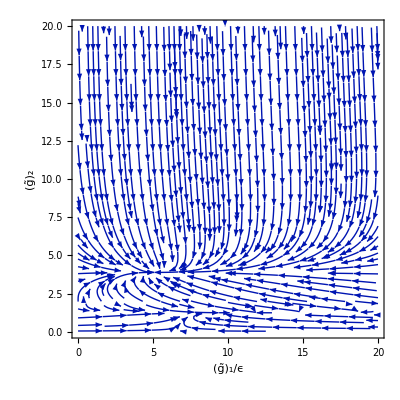

main_flow.pdf

```mathematica
range=20;
xfg=StreamPlot[{-beta1[y1,g2,4,1],-beta2[y1,g2,4,1]},{y1,0,range},{g2,0,range},StreamPoints->{Automatic,Scaled[0.005]},PlotRange-> {{0,range},{0,range}},FrameTicks->{{All,None},{All,None}},FrameTicksStyle-> Directive[FontSize-> 20,FontFamily->"Latin Modern Roman",FontColor->Black],BoundaryStyle->None,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["(g̃)_1/ϵ",FontFamily->"Times",FontSize->20,FontColor->Black],Style["(g̃)_2",FontFamily->"Times",FontSize->20,FontColor->Black]},
(*PlotLabel->Style["(a) g_((V^r)_⊥)/ℵ = 0",FontFamily->"Latin Modern Roman",FontSize->20,FontColor->Black],*)
ImagePadding->{{60,40},{70,10}}
]
Export["main_flow.pdf",xfg]
```

```mathematica
f[d_,g1_,g2_]:=1/(960 (-1+d) d (-4+g2^2)^3 π^2)g2 (46080 (-1+d) d-11520 (-1+d) d g2+64 (-120+d (661+d (-604+13 d))) g2^2-160 (-4+d) (-2+d) (5+3 d) g2^3-16 (-400+d (1083+d (-902+9 d))) g2^4-80 (-40+d (13+d (7+2 d))) g2^5+4 (-280+d (623+d (-572+19 d))) g2^6+10 (-40+d (26+d+d^2)) g2^7+d (-61+(124-13 d) d) g2^8) g1
```

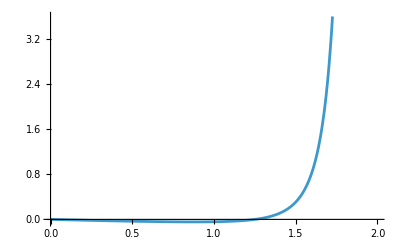

```mathematica
Plot[f[4,1,g2],{g2,0,2}]
```

## Asymmetric perturbations

## Computation for δZ_11 and δZ_13

```mathematica
LoopInt=-C1[2k-q,L,i1].G[q0,k-q,L].dband[k-q,LP].G[q0,k-q,L].C1[2k-q,L,i2]D1[w,q,i1,i2];
CT=-Subscript[δZ, 11]dband[k,LP]-Subscript[δZ, 13] dband[k,L];
CTObj1=TR[CT.dband[k,L],Contract-> False];
TrObj1=TR[LoopInt.dband[k,L],Contract-> False];
LEQ11131=LoopEvaluate[TrObj1,4,q0,q,qarr,L,LP,d,k0,k,{},{}]+LFC[CTObj1,L,LP,d,{}];
LEQ11131//TraditionalForm
CTObj2=TR[CT.dband[k,LP]];
TrObj2=TR[LoopInt.dband[k,LP]];
LEQ11132=LoopEvaluate[TrObj2,4,q0,q,qarr,L,LP,d,k0,k,{},{}]+LFC[CTObj2,L,LP,d,{}];
LEQ11132//TraditionalForm
```

LoopEvaluate((d^2 e^2 g^i1i2 (k-q)^i$12386033 k^i$12386039 (2 k-q)^j$12386031 (k-q)^j$12386033 (2 k-q)^j$12386035 k^j$12386039 (8 d m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) q0^2+8 d m^2 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 m^2 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 d m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033)) q0^2+8 m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033)) q0^2+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))))/(2 (1-d)^2 (d-1) (4 m^2 q0^2+(k-q)^4)^2 (w^2+v^2 q^4)),4,q0,q,qarr,L,LP,d,k0,k,{},{})-(4 k^102 ((d+1) δZ_11+(d-1) δZ_13))/(d-1)

LoopEvaluate((d^2 e^2 g^i1i2 (k-q)^i$12386033 k^i$12386131 (2 k-q)^j$12386031 (k-q)^j$12386033 (2 k-q)^j$12386035 k^j$12386131 (8 d m^2 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2+8 d m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) q0^2-8 d m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131)) q0^2+8 m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131)) q0^2+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))))/(2 (1-d)^2 (d-1) (4 m^2 q0^2+(k-q)^4)^2 (w^2+v^2 q^4)),4,q0,q,qarr,L,LP,d,k0,k,{},{})-(4 k^102 ((d-1) δZ_11+(d+1) δZ_13))/(d-1)

```mathematica
SOL1113=Collect2[Solve[LEQ11131==0&&LEQ11132==0,{Subscript[δZ, 11],Subscript[δZ, 13]}],q,Factoring-> FullSimplify];
SOL1113//TraditionalForm
FullSimplify[N[Collect2[SOL1113/.{d-> 4},q,Factoring-> FullSimplify]]]
```

{{δZ_11→1/(16 d k^102)(d^2-1) LoopEvaluate((d^2 e^2 g^i1i2 (k-q)^i$12386033 k^i$12386039 (2 k-q)^j$12386031 (k-q)^j$12386033 (2 k-q)^j$12386035 k^j$12386039 (8 d m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) q0^2+8 d m^2 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 m^2 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 d m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033)) q0^2+8 m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033)) q0^2+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))))/(2 (1-d)^2 (d-1) (4 m^2 q0^2+(k-q)^4)^2 (w^2+v^2 q^4)),4,q0,q,qarr,L,LP,d,k0,k,{},{})-1/(16 d k^102)(d-1)^2 LoopEvaluate((d^2 e^2 g^i1i2 (k-q)^i$12386033 k^i$12386131 (2 k-q)^j$12386031 (k-q)^j$12386033 (2 k-q)^j$12386035 k^j$12386131 (8 d m^2 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2+8 d m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) q0^2-8 d m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131)) q0^2+8 m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131)) q0^2+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))))/(2 (1-d)^2 (d-1) (4 m^2 q0^2+(k-q)^4)^2 (w^2+v^2 q^4)),4,q0,q,qarr,L,LP,d,k0,k,{},{}),δZ_13→1/(16 d k^102)(d^2-1) LoopEvaluate((d^2 e^2 g^i1i2 (k-q)^i$12386033 k^i$12386131 (2 k-q)^j$12386031 (k-q)^j$12386033 (2 k-q)^j$12386035 k^j$12386131 (8 d m^2 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2+8 d m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) q0^2-8 d m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131)) q0^2+8 m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131)) q0^2+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386131,j$12386131)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386131,j$12386131)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (LP(i$12386033,j$12386033)·LP(i$12386131,j$12386131))))/(2 (1-d)^2 (d-1) (4 m^2 q0^2+(k-q)^4)^2 (w^2+v^2 q^4)),4,q0,q,qarr,L,LP,d,k0,k,{},{})-1/(16 d k^102)(d-1)^2 LoopEvaluate((d^2 e^2 g^i1i2 (k-q)^i$12386033 k^i$12386039 (2 k-q)^j$12386031 (k-q)^j$12386033 (2 k-q)^j$12386035 k^j$12386039 (8 d m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) q0^2-8 m^2 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) q0^2+8 d m^2 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 m^2 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) q0^2-8 d m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033)) q0^2+8 m^2 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033)) q0^2+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·LP(i$12386033,j$12386033)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·LP(i$12386033,j$12386033)) (L(i$12386034,j$12386034)·L(i$12386039,j$12386039))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386039,j$12386039)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386039,j$12386039)) (L(i$12386034,j$12386034)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386034,j$12386034)) (L(i2,j$12386035)·L(i$12386032,j$12386032)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i$12386032,j$12386032)) (L(i2,j$12386035)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 k^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 q^j$12386032 k^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 k^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 q^i$12386034 k^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d k^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d q^i$12386032 k^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))+d k^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))-d q^i$12386032 q^i$12386034 q^j$12386032 q^j$12386034 (L(i1,j$12386031)·L(i2,j$12386035)) (L(i$12386032,j$12386032)·L(i$12386034,j$12386034)) (L(i$12386039,j$12386039)·LP(i$12386033,j$12386033))))/(2 (1-d)^2 (d-1) (4 m^2 q0^2+(k-q)^4)^2 (w^2+v^2 q^4)),4,q0,q,qarr,L,LP,d,k0,k,{},{})}}

{{δZ_11→1/k^102(0.234375 LoopEvaluate[(e^2 Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-1. q]] Pair[LorentzIndex[i$12386039],Momentum[k]] Pair[LorentzIndex[j$12386031],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386033],Momentum[k-1. q]] Pair[LorentzIndex[j$12386035],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386039],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+(Pair[LorentzIndex[i$12386032],Momentum[q]] ((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] ((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))+(Pair[LorentzIndex[i$12386032],Momentum[q]] (((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]+((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]+((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/((1. m^2 q0^2+0.25 Pair[Momentum[k-1. q],Momentum[k-1. q]]^2)^2 (w^2+v^2 Pair[Momentum[q],Momentum[q]]^2)),4.,q0,q,qarr,L,LP,4.,k0,k,{},{}]-0.140625 LoopEvaluate[(e^2 Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-1. q]] Pair[LorentzIndex[i$12386131],Momentum[k]] Pair[LorentzIndex[j$12386031],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386033],Momentum[k-1. q]] Pair[LorentzIndex[j$12386035],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386131],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+(Pair[LorentzIndex[i$12386032],Momentum[q]] ((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] ((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]))+(Pair[LorentzIndex[i$12386032],Momentum[q]] (((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]+((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]+((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]))/((1. m^2 q0^2+0.25 Pair[Momentum[k-1. q],Momentum[k-1. q]]^2)^2 (w^2+v^2 Pair[Momentum[q],Momentum[q]]^2)),4.,q0,q,qarr,L,LP,4.,k0,k,{},{}]),δZ_13→1/k^102(-0.140625 LoopEvaluate[(e^2 Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-1. q]] Pair[LorentzIndex[i$12386039],Momentum[k]] Pair[LorentzIndex[j$12386031],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386033],Momentum[k-1. q]] Pair[LorentzIndex[j$12386035],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386039],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+(Pair[LorentzIndex[i$12386032],Momentum[q]] ((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] ((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))+(Pair[LorentzIndex[i$12386032],Momentum[q]] (((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]+((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]+((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/((1. m^2 q0^2+0.25 Pair[Momentum[k-1. q],Momentum[k-1. q]]^2)^2 (w^2+v^2 Pair[Momentum[q],Momentum[q]]^2)),4.,q0,q,qarr,L,LP,4.,k0,k,{},{}]+0.234375 LoopEvaluate[(e^2 Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-1. q]] Pair[LorentzIndex[i$12386131],Momentum[k]] Pair[LorentzIndex[j$12386031],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386033],Momentum[k-1. q]] Pair[LorentzIndex[j$12386035],Momentum[2. k-1. q]] Pair[LorentzIndex[j$12386131],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] (0.444444 m^2 q0^2+(((Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[k]]+((Pair[LorentzIndex[i$12386032],Momentum[q]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[k]]+(Pair[LorentzIndex[i$12386032],Momentum[k]] (0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[q]] (-0.0740741 Pair[LorentzIndex[i$12386034],Momentum[k]]+0.0740741 Pair[LorentzIndex[i$12386034],Momentum[q]])) Pair[LorentzIndex[j$12386032],Momentum[q]]) Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+(Pair[LorentzIndex[i$12386032],Momentum[q]] ((Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])+Pair[LorentzIndex[i$12386032],Momentum[k]] ((Pair[LorentzIndex[i$12386034],Momentum[q]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[k]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[k]]+(Pair[LorentzIndex[i$12386034],Momentum[k]] (0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])+Pair[LorentzIndex[i$12386034],Momentum[q]] (-0.0740741 Pair[LorentzIndex[j$12386032],Momentum[k]]+0.0740741 Pair[LorentzIndex[j$12386032],Momentum[q]])) Pair[LorentzIndex[j$12386034],Momentum[q]])) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+0.0740741 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$123

## Corrections necessary below this line

## Computation for δZ_12 , δZ_14 and δZ_15

```mathematica
LoopInt=2C1[p+2q,L,i].G[w,p+q,L].C1[p+2q,L,i].G[w,q,L].dband[q,LP].G[w,q,L];
TrObj=TR[LoopInt];
LE=LoopEvaluate[TrObj,4,w,q,qarr,L,LP,p0,p,{}];
LE//TraditionalForm
CTObj=-Subscript[δZ, 15]LFC[SPd[p,p](MTd[i,i]SPd[p,p]-FVd[p,i]FVd[p,i]),L,LP];
LEQ15=LE+CTObj;
LEQ15//TraditionalForm
```

LoopEvaluate((2 d √(-d/(1-d)) √(d/(d-1)) e^2 m q^i$12430037 (p+2 q)^j$12430033 (p+2 q)^j$12430035 q^j$12430037 (8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) w^2-8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) w^2-8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) w^2+8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) w^2+8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037)) w^2-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))))/((1-d) (d-1) (4 m^2 w^2+q^4)^2 (4 m^2 w^2+(p+q)^4)),4,w,q,qarr,L,LP,p0,p,{})

LoopEvaluate((2 d √(-d/(1-d)) √(d/(d-1)) e^2 m q^i$12430037 (p+2 q)^j$12430033 (p+2 q)^j$12430035 q^j$12430037 (8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) w^2-8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) w^2-8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) w^2+8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) w^2+8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037)) w^2-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))))/((1-d) (d-1) (4 m^2 w^2+q^4)^2 (4 m^2 w^2+(p+q)^4)),4,w,q,qarr,L,LP,p0,p,{})-LFC(p^2 (g^ii p^2-(p^i)^2),L,LP) δZ_15

```mathematica
SOL15=Collect2[Solve[LEQ15==0,Subscript[δZ, 15]],q,Factoring-> FullSimplify];
SOL15//TraditionalForm
Collect2[SOL15/.{d-> 4},q,Factoring-> FullSimplify]
```

{{δZ_15→1/(LFC(p^2 (g^ii p^2-(p^i)^2),L,LP))LoopEvaluate((2 √(-1/(1-d)) (1/(d-1))^(3/2) d^2 e^2 m q^i$12430037 (p+2 q)^j$12430033 (p+2 q)^j$12430035 q^j$12430037 (8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2-8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) w^2+8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) w^2-8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) w^2-8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) w^2+8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) w^2+8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) w^2-8 d m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 p^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430034 p^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 p^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2-8 d m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 m^2 q^i$12430034 q^j$12430034 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430036 q^j$12430036 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037)) w^2+8 d m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037)) w^2-8 m^2 q^i$12430038 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037)) w^2-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·LP(i$12430037,j$12430037)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·LP(i$12430037,j$12430037)) (L(i$12430036,j$12430036)·L(i$12430038,j$12430038))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430038,j$12430038)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430038,j$12430038)) (L(i$12430036,j$12430036)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430036,j$12430036)) (L(i,j$12430035)·L(i$12430034,j$12430034)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))-d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i$12430034,j$12430034)) (L(i,j$12430035)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 p^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d p^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))+d q^i$12430034 q^i$12430036 q^i$12430038 q^j$12430034 q^j$12430036 q^j$12430038 (L(i,j$12430033)·L(i,j$12430035)) (L(i$12430034,j$12430034)·L(i$12430036,j$12430036)) (L(i$12430038,j$12430038)·LP(i$12430037,j$12430037))))/((1-d) (4 m^2 w^2+q^4)^2 (4 m^2 w^2+(p+q)^4)),4,w,q,qarr,L,LP,p0,p,{})}}

{{δZ_15→LoopEvaluate[-((32 e^2 m Pair[LorentzIndex[i$12430037],Momentum[q]] Pair[LorentzIndex[j$12430033],Momentum[p+2 q]] Pair[LorentzIndex[j$12430035],Momentum[p+2 q]] Pair[LorentzIndex[j$12430037],Momentum[q]] (24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]]-24 m^2 w^2 Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]]-24 m^2 w^2 Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]]-24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-24 m^2 w^2 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[LP[i$12430037,j$12430037],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[L[i$12430038,j$12430038],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430038,j$12430038],D]] Pair[Momentum[L[i$12430036,j$12430036],D],Momentum[LP[i$12430037,j$12430037],D]]+24 m^2 w^2 Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]-4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i$12430034,j$12430034],D]] Pair[Momentum[L[i,j$12430035],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[p]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[p]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]+4 Pair[LorentzIndex[i$12430034],Momentum[q]] Pair[LorentzIndex[i$12430036],Momentum[q]] Pair[LorentzIndex[i$12430038],Momentum[q]] Pair[LorentzIndex[j$12430034],Momentum[q]] Pair[LorentzIndex[j$12430036],Momentum[q]] Pair[LorentzIndex[j$12430038],Momentum[q]] Pair[Momentum[L[i,j$12430033],D],Momentum[L[i,j$12430035],D]] Pair[Momentum[L[i$12430034,j$12430034],D],Momentum[L[i$12430036,j$12430036],D]] Pair[Momentum[L[i$12430038,j$12430038],D],Momentum[LP[i$12430037,j$12430037],D]]))/(27 (4 m^2 w^2+Pair[Momentum[q],Momentum[q]]^2)^2 (4 m^2 w^2+Pair[Momentum[p+q],Momentum[p+q]]^2))),4,w,q,qarr,L,LP,p0,p,{}]/LFC[Pair[Momentum[p],Momentum[p]] (-Pair[LorentzIndex[i],Momentum[p]]^2+Pair[LorentzIndex[i],LorentzIndex[i]] Pair[Momentum[p],Momentum[p]]),L,LP]}}

```mathematica
LoopInt=2(C1[2q,L,i]).G[w+z,q,L].(C1[2q,L,i]).G[w,q,L].dband[q,LP].G[w,q,L];
TrObj=TR[LoopInt];
LE=LoopEvaluate[TrObj,2,w,q,qarr,L,LP,z,p,{}];
LE//TraditionalForm
CTObj=-d Subscript[δZ, 14] z^2;
LEQ14=LE+CTObj;
LEQ14//TraditionalForm
```

LoopEvaluate((8 d √(-d/(1-d)) √(d/(d-1)) e^2 m q^i$12430288 q^j$12430284 q^j$12430286 q^j$12430288 (8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) m^2-8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) m^2+8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2+8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2-8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) m^2+8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))))/((1-d) (d-1) (4 m^2 w^2+q^4)^2 (4 w^2 m^2+4 z^2 m^2+8 w z m^2+q^4)),2,w,q,qarr,L,LP,z,p,{})

LoopEvaluate((8 d √(-d/(1-d)) √(d/(d-1)) e^2 m q^i$12430288 q^j$12430284 q^j$12430286 q^j$12430288 (8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) m^2-8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) m^2+8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2+8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2-8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) m^2+8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))))/((1-d) (d-1) (4 m^2 w^2+q^4)^2 (4 w^2 m^2+4 z^2 m^2+8 w z m^2+q^4)),2,w,q,qarr,L,LP,z,p,{})-d z^2 δZ_14

```mathematica
SOL14=Collect2[Solve[LEQ14==0,Subscript[δZ, 14]],q,Factoring-> FullSimplify];
SOL14//TraditionalForm
Collect2[SOL/.{d-> 4},q,Factoring-> FullSimplify]
```

{{δZ_14→1/(d z^2)LoopEvaluate((8 √(-1/(1-d)) (1/(d-1))^(3/2) d^2 e^2 m q^i$12430288 q^j$12430284 q^j$12430286 q^j$12430288 (8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) m^2-8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) m^2+8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2+8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) m^2-8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2-8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) m^2+8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) m^2-8 d w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) m^2+8 w^2 q^i$12430285 q^j$12430285 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430287 q^j$12430287 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288)) m^2+8 d w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-8 w^2 q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2+8 d w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-8 w z q^i$12430289 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288)) m^2-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·LP(i$12430288,j$12430288)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·LP(i$12430288,j$12430288)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·LP(i$12430288,j$12430288)) (L(i$12430287,j$12430287)·L(i$12430289,j$12430289))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430289,j$12430289)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·L(i$12430289,j$12430289)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·L(i$12430289,j$12430289)) (L(i$12430287,j$12430287)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430287,j$12430287)) (L(i,j$12430286)·L(i$12430285,j$12430285)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))-d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i$12430285,j$12430285)) (L(i,j$12430286)·L(i$12430287,j$12430287)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))+d q^i$12430285 q^i$12430287 q^i$12430289 q^j$12430285 q^j$12430287 q^j$12430289 (L(i,j$12430284)·L(i,j$12430286)) (L(i$12430285,j$12430285)·L(i$12430287,j$12430287)) (L(i$12430289,j$12430289)·LP(i$12430288,j$12430288))))/((1-d) (4 m^2 w^2+q^4)^2 (4 w^2 m^2+4 z^2 m^2+8 w z m^2+q^4)),2,w,q,qarr,L,LP,z,p,{})}}

SOL

```mathematica
SOL12={Subscript[δZ, 12]:>0}
```

{δZ_12:>0}

## Computation for δZ_21 and δZ_23

```mathematica
LoopInt=-C1[2p-q,L,i1].G[w,p-q,L].C1[2p-q,L,i4]D1[w,q,i1,i2]CubeAniso[q,qarr,t,u,i2,i3]D1[w,q,i3,i4];
CT=-Subscript[δZ, 21]dband[p,LP]-Subscript[δZ, 23] dband[p,L];
CTObj1=TR[CT.dband[p,L]];
TrObj1=TR[LoopInt.dband[p,L]];
LEQ21231=LoopEvaluate[TrObj1,4,w,q,qarr,L,LP,p0,p,{t,u}]+LFC[CTObj1,L,LP];
LEQ21231//TraditionalForm
CTObj2=TR[CT.dband[p,LP]];
TrObj2=TR[LoopInt.dband[p,LP]];
LEQ21232=LoopEvaluate[TrObj2,4,w,q,qarr,L,LP,p0,p,{t,u}]+LFC[CTObj2,L,LP];
LEQ21232//TraditionalForm
```

LoopEvaluate(-((d √(-d/(1-d)) √(d/(d-1)) e^2 p^i$12430393 p^j$12430393 (p^i$12430388-q^i$12430388) (2 p-q)^j$12430387 (p^j$12430388-q^j$12430388) (2 p-q)^j$12430389 (q^i1 q^i4 g^tu-q^2 g^i1i4 g^tu-q^i4 q^t g^i1u-q^i1 q^u g^i4t+q^t q^u g^i1i4+q^2 g^i1u g^i4t) qarr(q,{t,u}) ((L(i1,j$12430387)·L(i$12430393,j$12430393)) (L(i4,j$12430389)·L(i$12430388,j$12430388))+(L(i1,j$12430387)·L(i$12430388,j$12430388)) (L(i4,j$12430389)·L(i$12430393,j$12430393))-(L(i1,j$12430387)·L(i4,j$12430389)) (L(i$12430388,j$12430388)·L(i$12430393,j$12430393))))/(2 (1-d) m (q^4 v^2+w^2)^2 (4 (p·q)^2+4 m^2 w^2+2 p^2 q^2-4 p^2 (p·q)-4 q^2 (p·q)+p^4+q^4))),4,w,q,qarr,L,LP,p0,p,{t,u})+LFC(-2 √(-d/(1-d)) √(d/(d-1)) p^i$12430392 p^j$12430392 (δZ_21 p^i$12430390 p^j$12430390 (L(i$12430392,j$12430392)·LP(i$12430390,j$12430390))+δZ_23 p^i$12430391 p^j$12430391 (L(i$12430391,j$12430391)·L(i$12430392,j$12430392))),L,LP)

LoopEvaluate(-((d √(-d/(1-d)) √(d/(d-1)) e^2 p^i$12430395 p^j$12430395 (p^i$12430388-q^i$12430388) (2 p-q)^j$12430387 (p^j$12430388-q^j$12430388) (2 p-q)^j$12430389 (q^i1 q^i4 g^tu-q^2 g^i1i4 g^tu-q^i4 q^t g^i1u-q^i1 q^u g^i4t+q^t q^u g^i1i4+q^2 g^i1u g^i4t) qarr(q,{t,u}) ((L(i4,j$12430389)·L(i$12430388,j$12430388)) (L(i1,j$12430387)·LP(i$12430395,j$12430395))+(L(i1,j$12430387)·L(i$12430388,j$12430388)) (L(i4,j$12430389)·LP(i$12430395,j$12430395))-(L(i1,j$12430387)·L(i4,j$12430389)) (L(i$12430388,j$12430388)·LP(i$12430395,j$12430395))))/(2 (1-d) m (q^4 v^2+w^2)^2 (4 (p·q)^2+4 m^2 w^2+2 p^2 q^2-4 p^2 (p·q)-4 q^2 (p·q)+p^4+q^4))),4,w,q,qarr,L,LP,p0,p,{t,u})+LFC(-2 √(-d/(1-d)) √(d/(d-1)) p^i$12430394 p^j$12430394 (δZ_21 p^i$12430390 p^j$12430390 (LP(i$12430390,j$12430390)·LP(i$12430394,j$12430394))+δZ_23 p^i$12430391 p^j$12430391 (L(i$12430391,j$12430391)·LP(i$12430394,j$12430394))),L,LP)

```mathematica
LEQT21231=Collect2[Cancel[Collect2[LFC[LEQ21231//.{u-> t,Pair[LorentzIndex[t_,d],Momentum[p,d]]^4:> Sum[Subscript[p, t]^4,{t,1,d}], Pair[LorentzIndex[t_,d],LorentzIndex[t_,d]] Pair[LorentzIndex[t_,d],Momentum[p,d]]^2:> Pair[LorentzIndex[t,d],Momentum[p,d]]^2},L,LP],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]
LEQP21231=Coefficient[LEQT21231,p,4]
```

LFC[LFC[-2 √(-d/(1-d)) √(d/(-1+d)) Pair[LorentzIndex[i$12430392,d],Momentum[p,d]] Pair[LorentzIndex[j$12430392,d],Momentum[p,d]] (Pair[LorentzIndex[i$12430390,d],Momentum[p,d]] Pair[LorentzIndex[j$12430390,d],Momentum[p,d]] Pair[Momentum[L[i$12430392,j$12430392],D],Momentum[LP[i$12430390,j$12430390],D]] δZ_21+Pair[LorentzIndex[i$12430391,d],Momentum[p,d]] Pair[LorentzIndex[j$12430391,d],Momentum[p,d]] Pair[Momentum[L[i$12430391,j$12430391],D],Momentum[L[i$12430392,j$12430392],D]] δZ_23),L,LP]+LoopEvaluate[-((d √(-d/(1-d)) √(d/(-1+d)) e^2 (Pair[LorentzIndex[i$12430388,d],Momentum[p,d]]-Pair[LorentzIndex[i$12430388,d],Momentum[q,d]]) Pair[LorentzIndex[i$12430393,d],Momentum[p,d]] Pair[LorentzIndex[j$12430387,d],Momentum[2 p-q,d]] (Pair[LorentzIndex[j$12430388,d],Momentum[p,d]]-Pair[LorentzIndex[j$12430388,d],Momentum[q,d]]) Pair[LorentzIndex[j$12430389,d],Momentum[2 p-q,d]] Pair[LorentzIndex[j$12430393,d],Momentum[p,d]] (Pair[LorentzIndex[i1,d],Momentum[q,d]] Pair[LorentzIndex[i4,d],Momentum[q,d]] Pair[LorentzIndex[t,d],LorentzIndex[t,d]]-Pair[LorentzIndex[i1,d],Momentum[q,d]] Pair[LorentzIndex[i4,d],LorentzIndex[t,d]] Pair[LorentzIndex[t,d],Momentum[q,d]]-Pair[LorentzIndex[i1,d],LorentzIndex[t,d]] Pair[LorentzIndex[i4,d],Momentum[q,d]] Pair[LorentzIndex[t,d],Momentum[q,d]]+Pair[LorentzIndex[i1,d],LorentzIndex[i4,d]] Pair[LorentzIndex[t,d],Momentum[q,d]]^2+Pair[LorentzIndex[i1,d],LorentzIndex[t,d]] Pair[LorentzIndex[i4,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]]-Pair[LorentzIndex[i1,d],LorentzIndex[i4,d]] Pair[LorentzIndex[t,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12430387],D],Momentum[L[i$12430393,j$12430393],D]] Pair[Momentum[L[i4,j$12430389],D],Momentum[L[i$12430388,j$12430388],D]]+Pair[Momentum[L[i1,j$12430387],D],Momentum[L[i$12430388,j$12430388],D]] Pair[Momentum[L[i4,j$12430389],D],Momentum[L[i$12430393,j$12430393],D]]-Pair[Momentum[L[i1,j$12430387],D],Momentum[L[i4,j$12430389],D]] Pair[Momentum[L[i$12430388,j$12430388],D],Momentum[L[i$12430393,j$12430393],D]]) qarr[q,{t,t}])/(2 (1-d) m (4 m^2 w^2+Pair[Momentum[p,d],Momentum[p,d]]^2-4 Pair[Momentum[p,d],Momentum[p,d]] Pair[Momentum[p,d],Momentum[q,d]]+4 Pair[Momentum[p,d],Momentum[q,d]]^2+2 Pair[Momentum[p,d],Momentum[p,d]] Pair[Momentum[q,d],Momentum[q,d]]-4 Pair[Momentum[p,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]]^2) (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)^2)),4,w,q,qarr,L,LP,p0,p,{t,t}],L,LP]

0

Sum::vloc: The variable #1 cannot be localized so that it can be assigned to numerical values.

```mathematica
LEQT21232=Collect2[Cancel[Collect2[LFC[LEQ21232//.{u-> t,Pair[LorentzIndex[t_,d],Momentum[p,d]]^4:> Sum[Subscript[p, t]^4,{t,1,d}], Pair[LorentzIndex[t_,d],LorentzIndex[t_,d]] Pair[LorentzIndex[t_,d],Momentum[p,d]]^2:> Pair[LorentzIndex[t,d],Momentum[p,d]]^2},L,LP],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]],{p,q,Sum[Subscript[p, #]^4,{#,1,d}],Subscript[δZ, 21],Subscript[δZ, 23]},Factoring-> FullSimplify]
LEQP21232=Coefficient[LEQT21232,p,4]
```

LFC[LFC[-2 √(-d/(1-d)) √(d/(-1+d)) Pair[LorentzIndex[i$12430394,d],Momentum[p,d]] Pair[LorentzIndex[j$12430394,d],Momentum[p,d]] (Pair[LorentzIndex[i$12430390,d],Momentum[p,d]] Pair[LorentzIndex[j$12430390,d],Momentum[p,d]] Pair[Momentum[LP[i$12430390,j$12430390],D],Momentum[LP[i$12430394,j$12430394],D]] δZ_21+Pair[LorentzIndex[i$12430391,d],Momentum[p,d]] Pair[LorentzIndex[j$12430391,d],Momentum[p,d]] Pair[Momentum[L[i$12430391,j$12430391],D],Momentum[LP[i$12430394,j$12430394],D]] δZ_23),L,LP]+LoopEvaluate[-((d √(-d/(1-d)) √(d/(-1+d)) e^2 (Pair[LorentzIndex[i$12430388,d],Momentum[p,d]]-Pair[LorentzIndex[i$12430388,d],Momentum[q,d]]) Pair[LorentzIndex[i$12430395,d],Momentum[p,d]] Pair[LorentzIndex[j$12430387,d],Momentum[2 p-q,d]] (Pair[LorentzIndex[j$12430388,d],Momentum[p,d]]-Pair[LorentzIndex[j$12430388,d],Momentum[q,d]]) Pair[LorentzIndex[j$12430389,d],Momentum[2 p-q,d]] Pair[LorentzIndex[j$12430395,d],Momentum[p,d]] (Pair[LorentzIndex[i1,d],Momentum[q,d]] Pair[LorentzIndex[i4,d],Momentum[q,d]] Pair[LorentzIndex[t,d],LorentzIndex[t,d]]-Pair[LorentzIndex[i1,d],Momentum[q,d]] Pair[LorentzIndex[i4,d],LorentzIndex[t,d]] Pair[LorentzIndex[t,d],Momentum[q,d]]-Pair[LorentzIndex[i1,d],LorentzIndex[t,d]] Pair[LorentzIndex[i4,d],Momentum[q,d]] Pair[LorentzIndex[t,d],Momentum[q,d]]+Pair[LorentzIndex[i1,d],LorentzIndex[i4,d]] Pair[LorentzIndex[t,d],Momentum[q,d]]^2+Pair[LorentzIndex[i1,d],LorentzIndex[t,d]] Pair[LorentzIndex[i4,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]]-Pair[LorentzIndex[i1,d],LorentzIndex[i4,d]] Pair[LorentzIndex[t,d],LorentzIndex[t,d]] Pair[Momentum[q,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12430387],D],Momentum[LP[i$12430395,j$12430395],D]] Pair[Momentum[L[i4,j$12430389],D],Momentum[L[i$12430388,j$12430388],D]]+Pair[Momentum[L[i1,j$12430387],D],Momentum[L[i$12430388,j$12430388],D]] Pair[Momentum[L[i4,j$12430389],D],Momentum[LP[i$12430395,j$12430395],D]]-Pair[Momentum[L[i1,j$12430387],D],Momentum[L[i4,j$12430389],D]] Pair[Momentum[L[i$12430388,j$12430388],D],Momentum[LP[i$12430395,j$12430395],D]]) qarr[q,{t,t}])/(2 (1-d) m (4 m^2 w^2+Pair[Momentum[p,d],Momentum[p,d]]^2-4 Pair[Momentum[p,d],Momentum[p,d]] Pair[Momentum[p,d],Momentum[q,d]]+4 Pair[Momentum[p,d],Momentum[q,d]]^2+2 Pair[Momentum[p,d],Momentum[p,d]] Pair[Momentum[q,d],Momentum[q,d]]-4 Pair[Momentum[p,d],Momentum[q,d]] Pair[Momentum[q,d],Momentum[q,d]]+Pair[Momentum[q,d],Momentum[q,d]]^2) (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)^2)),4,w,q,qarr,L,LP,p0,p,{t,t}],L,LP]

0

Sum::vloc: The variable #1 cannot be localized so that it can be assigned to numerical values.

General::stop: Further output of Sum::vloc will be suppressed during this calculation.

Sum::vloc: The variable #1 cannot be localized so that it can be assigned to numerical values.

```mathematica
SOL2123=Collect2[Solve[LEQP21231==0&&LEQP21232==0,{Subscript[δZ, 21],Subscript[δZ, 23]}],q,Factoring-> FullSimplify];
SOL2123//TraditionalForm
FullSimplify[N[Collect2[SOL2123/.{d-> 4},q,Factoring-> FullSimplify]]]
```

{{}}

{{}}

```mathematica
Subscript[δZ, 21]
```

δZ_21

```mathematica
Flatten[Join[SOL1113,SOL12,SOL14,SOL15,SOL2123]]
```

{δZ_11→1/(16 d k^102)(-1+d^2) LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386039,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386039,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]]-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/(2 (1-d)^2 (-1+d) (4 m^2 q0^2+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}]-1/(16 d k^102)(-1+d)^2 LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386131,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386131,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i

## Anomalous mixing matrix

```mathematica
ZMP={{Subscript[δZ, 11],Subscript[δZ, 12],Subscript[δZ, 13],Subscript[δZ, 14],Subscript[δZ, 15]},{Subscript[δZ, 21],Subscript[δZ, 22],Subscript[δZ, 23],Subscript[δZ, 24],Subscript[δZ, 25]},{Subscript[δZ, 31],Subscript[δZ, 32],Subscript[δZ, 33],Subscript[δZ, 34],Subscript[δZ, 35]},{Subscript[δZ, 41],Subscript[δZ, 42],Subscript[δZ, 43],Subscript[δZ, 44],Subscript[δZ, 45]},{Subscript[δZ, 51],Subscript[δZ, 52],Subscript[δZ, 53],Subscript[δZ, 54],Subscript[δZ, 55]}}/.Flatten[Join[SOL1113,SOL12,SOL14,SOL15,SOL2123]];
ZM=FullSimplify[IdentityMatrix[5]+ZMP/.{Subscript[δZ, x_]-> 0}];
ZM//MatrixForm
ZLM=FullSimplify[Collect2[Eigenvalues[ZM],q,FullSimplify]/.{1/q^4-> 1/(8 π^2 ϵ)}]
```

(1+((-1+d^2) LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386039,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386039,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] (8 (-1+d) m^2 q0^2+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-8 (-1+d) m^2 q0^2-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/(2 (-1+d)^3 (4 m^2 q0^2+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}]-(-1+d)^2 LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386131,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386131,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] (8 (-1+d) m^2 q0^2+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-8 (-1+d) m^2 q0^2-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]))/(2 (-1+d)^3 (4 m^2 q0^2+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}])/(16 d k^102) | 0 | (-(-1+d)^2 LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386039,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386039,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] (8 (-1+d) m^2 q0^2+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-8 (-1+d) m^2 q0^2-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/(2 (-1+d)^3 (4 m^2 q0^2+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}]+(-1+d^2) LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386131,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386131,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum

{1,1,1,1,1+1/(16 d k^102)((-1+d^2) LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386039,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386039,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] (8 (-1+d) m^2 q0^2+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-8 (-1+d) m^2 q0^2-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/(2 (-1+d)^3 (4 m^2 q0^2+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}]-(-1+d)^2 LoopEvaluate[(d^2 e^2 Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386131,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386131,d],Momentum[k,d]] (-8 m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+8 d m^2 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] (8 (-1+d) m^2 q0^2+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-8 (-1+d) m^2 q0^2-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]))/(2 (-1+d)^3 (4 m^2 q0^2+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}])}

```mathematica
ZLMP[g1_,g2_]:=FullSimplify[ZLM//.{e^2-> g1/m,m-> 1/(g2 √v)}]
```

```mathematica
ZLMP[g1,g2]
```

{1,1,1,1,1+1/(16 d k^102)((-1+d^2) LoopEvaluate[(d^2 g1 g2 √v Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386039,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386039,d],Momentum[k,d]] (-1/(g2^2 v)8 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+1/(g2^2 v)8 d q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] ((8 (-1+d) q0^2)/(g2^2 v)+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-(8 (-1+d) q0^2)/(g2^2 v)-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/(2 (-1+d)^3 ((4 q0^2)/(g2^2 v)+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}]-(-1+d)^2 LoopEvaluate[(d^2 g1 g2 √v Pair[LorentzIndex[i1,d],LorentzIndex[i2,d]] Pair[LorentzIndex[i$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[i$12386131,d],Momentum[k,d]] Pair[LorentzIndex[j$12386031,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386033,d],Momentum[k-q,d]] Pair[LorentzIndex[j$12386035,d],Momentum[2 k-q,d]] Pair[LorentzIndex[j$12386131,d],Momentum[k,d]] (-1/(g2^2 v)8 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+1/(g2^2 v)8 d q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] ((8 (-1+d) q0^2)/(g2^2 v)+d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[k,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[k,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[k,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-d Pair[LorentzIndex[i$12386032,d],Momentum[k,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+d Pair[LorentzIndex[i$12386032,d],Momentum[q,d]] Pair[LorentzIndex[i$12386034,d],Momentum[q,d]] Pair[LorentzIndex[j$12386032,d],Momentum[q,d]] Pair[LorentzIndex[j$12386034,d],Momentum[q,d]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+(d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-(8 (-1+d) q0^2)/(g2^2 v)-d (Pair[LorentzIndex[i$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[i$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[i$12386034,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386032,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386032,d],Momentum[q,d]]) (Pair[LorentzIndex[j$12386034,d],Momentum[k,d]]-Pair[LorentzIndex[j$12386034,d],Momentum[q,d]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]))/(2 (-1+d)^3 ((4 q0^2)/(g2^2 v)+Pair[Momentum[k-q,d],Momentum[k-q,d]]^2)^2 (w^2+v^2 Pair[Momentum[q,d],Momentum[q,d]]^2)),4,q0,q,qarr,L,LP,d,k0,k,{},{}])}

```mathematica
2+{1,1,2}
```

{3,3,4}

```mathematica
{3,3,4}{C1,C2,C3}
```

{3 C1,3 C2,4 C3}

```mathematica
AnomBeta[Z_,C_,RegDim_,ϵ_,g1_,g2_]:=Module[{beta1,beta2},beta1=-ϵ;beta2=0;FullSimplify[-(RegDim+beta1 D[Z,g1]+beta2 D[Z,g2])C]]
```

```mathematica
AnomBeta[ZLMP[g1,g2],{C1,C2,C3,C4,C5},0,ϵ,g1,g2]/.{g1-> 4.3474 ϵ,g2-> 2.42705,d-> 4}
```

{0,0,0,0,(0.0112363 C5 √v ϵ Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-q]] Pair[LorentzIndex[j$12386031],Momentum[2 k-q]] Pair[LorentzIndex[j$12386033],Momentum[k-q]] Pair[LorentzIndex[j$12386035],Momentum[2 k-q]] (15 Pair[LorentzIndex[i$12386039],Momentum[k]] Pair[LorentzIndex[j$12386039],Momentum[k]] (1/v 4.07431 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] ((4.07431 q0^2)/v+4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+(4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-(4.07431 q0^2)/v-4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]) LoopEvaluate^(1,0,0,0,0,0,0,0,0,0)[(3.12633 √v ϵ Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-q]] Pair[LorentzIndex[i$12386039],Momentum[k]] Pair[LorentzIndex[j$12386031],Momentum[2 k-q]] Pair[LorentzIndex[j$12386033],Momentum[k-q]] Pair[LorentzIndex[j$12386035],Momentum[2 k-q]] Pair[LorentzIndex[j$12386039],Momentum[k]] (1/v 4.07431 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] ((4.07431 q0^2)/v+4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])+4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]]-Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[L[i$12386039,j$12386039],D]]))-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386039,j$12386039],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+(4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-(4.07431 q0^2)/v-4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[L[i$12386039,j$12386039],D],Momentum[LP[i$12386033,j$12386033],D]]))/(((0.679051 q0^2)/v+Pair[Momentum[k-q],Momentum[k-q]]^2)^2 (w^2+v^2 Pair[Momentum[q],Momentum[q]]^2)),4,q0,q,qarr,L,LP,4,k0,k,{},{}]-9 Pair[LorentzIndex[i$12386131],Momentum[k]] Pair[LorentzIndex[j$12386131],Momentum[k]] (1/v 4.07431 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386131,j$12386131],D]] (Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] ((4.07431 q0^2)/v+4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])-4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) (Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386033,j$12386033],D]]))-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i$12386034,j$12386034],D],Momentum[LP[i$12386131,j$12386131],D]]+(4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) (Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386032,j$12386032],D]]-Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386032,j$12386032],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]])+Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i2,j$12386035],D]] (-(4.07431 q0^2)/v-4 (Pair[LorentzIndex[i$12386032],Momentum[k]]-Pair[LorentzIndex[i$12386032],Momentum[q]]) (Pair[LorentzIndex[i$12386034],Momentum[k]]-Pair[LorentzIndex[i$12386034],Momentum[q]]) (Pair[LorentzIndex[j$12386032],Momentum[k]]-Pair[LorentzIndex[j$12386032],Momentum[q]]) (Pair[LorentzIndex[j$12386034],Momentum[k]]-Pair[LorentzIndex[j$12386034],Momentum[q]]) Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]])) Pair[Momentum[LP[i$12386033,j$12386033],D],Momentum[LP[i$12386131,j$12386131],D]]) LoopEvaluate^(1,0,0,0,0,0,0,0,0,0)[(3.12633 √v ϵ Pair[LorentzIndex[i1],LorentzIndex[i2]] Pair[LorentzIndex[i$12386033],Momentum[k-q]] Pair[LorentzIndex[i$12386131],Momentum[k]] Pair[LorentzIndex[j$12386031],Momentum[2 k-q]] Pair[LorentzIndex[j$12386033],Momentum[k-q]] Pair[LorentzIndex[j$12386035],Momentum[2 k-q]] Pair[LorentzIndex[j$12386131],Momentum[k]] (1/v 4.07431 q0^2 Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[L[i$12386034,j$12386034],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[LP[i$12386131,j$12386131],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386033,j$12386033],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[k]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032],Momentum[q]] Pair[LorentzIndex[i$12386034],Momentum[q]] Pair[LorentzIndex[j$12386032],Momentum[k]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]+4 Pair[LorentzIndex[i$12386032],Momentum[k]] Pair[LorentzIndex[i$12386034],Momentum[k]] Pair[LorentzIndex[j$12386032],Momentum[q]] Pair[LorentzIndex[j$12386034],Momentum[q]] Pair[Momentum[L[i1,j$12386031],D],Momentum[LP[i$12386033,j$12386033],D]] Pair[Momentum[L[i2,j$12386035],D],Momentum[L[i$12386034,j$12386034],D]] Pair[Momentum[L[i$12386032,j$12386032],D],Momentum[LP[i$12386131,j$12386131],D]]-4 Pair[LorentzIndex[i$12386032